## VTI Comparison with FD

#### Compute data in x-ω space

```mathematica
$MinPrecision=15
```

15

```mathematica
<<ThinLayer`
```

```mathematica
setlayer[]:=Module[{},
tlSetLayer[1,tlCijFromThomsen[2,1,0.01,-0.05,2]];
tlSetLayer[2,tlCijFromThomsen[3,1.5,0.02,0.01,3]];
]
```

```mathematica
setlayer[]
```

```mathematica
(*BZV={N@BesselJZero[0,Range[30000]],N@BesselJZero[1,Range[30000]]};*)
```

```mathematica
(*Export[NotebookDirectory[]<>"BesselZeros.mc",Compress[BZV],"String"]*)
```

C:\Users\yuriyi\Dropbox\Study_etc\NTNU\Anisotropy\Mathematica\PETROMAKS\PM2-codes\numerics\BesselZeros.mc

```mathematica
BZV=Uncompress@Import[NotebookDirectory[]<>"BesselZeros.mc","String"]
```

FindMinimum::acceptlev: Solved to acceptable level.

Time taken to calculate slowness limiting values functions: 668.73 sec

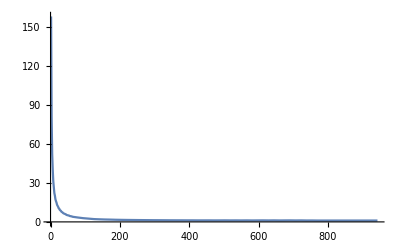

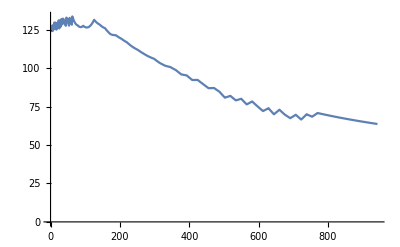

Time taken to calculate inverse Hankel transform: 4482.91 sec

```mathematica
Module[
{r=.5,layers,zs,zr,overburden,model,pcrit,dList,integrandp,toHTp,HTvec,Nfreq,deltafreq,maxfreq,ωList,toHTk,u,ur,uz,timingHT,timingPMAX,timingBessel,dp,pI,T,HW,BV},

(* ==== MODEL PARAMETERS ====*)
zs=.1;
zr=.7;
overburden=1;
layers={2};
model={overburden,Sequence@@layers};
dList={0,0};

pcrit=Flatten[N@(({#[[1]],#[[4]]}/(#[[-1]]))^(-1/2))&/@tlGetStiffness[model]];

Nfreq=600;
maxfreq=150.;
deltafreq=maxfreq/Nfreq;
ωList=2Pi Range[deltafreq,maxfreq,deltafreq]//N;
freqvec=ωList;

ωI=Log[50.]deltafreq/50;

(*With[{ω=ωList[[100]],p=RandomReal[{0,1.5}]},

Print[{BesselJ[0,p ω r],BesselJ[1,p ω r]} p tlResponse[model,dList,p,ω,zs,zr]];

Print[tlResponseVforce[model,dList,p,ω,zs,zr,r]];

]*)


(*===IDHT===*)
HW[p_,ω_]:=Module[{p1=0,p2=.5Min@Abs@pcrit ω,p3=1.5Max@Abs@pcrit ω,p4=2Max@Abs@pcrit ω},
Piecewise[{{1/2(1+Cos[Pi (p2-p)/(p2-p1)]),p≥p1&&p2≥p},{1,p>p2&&p3>p},{1/2(1+Cos[Pi (p-p3)/(p4-p3)]),p≥p3&&p4≥p}}]
];

HW[k_,ω_]=1;

uz[k_,ω_]:=HW[k,ω]tlResponse[model,dList,k/ω,ω+I ωI,zs,zr][[1]]/(ω+I ωI)^2;
ur[k_,ω_]:=HW[k,ω]tlResponse[model,dList,k/ω,ω+I ωI,zs,zr][[2]]/(ω+I ωI)^2;

Module[{np=20000,BesselVector,rmax,pmax,BesselTakeUpToN},

BesselVector=BZV[[;;,1;;np]];

BesselTakeUpToN[w_]=Ceiling[Interpolation[{{ωList[[1]],10000},{ωList[[-1]],np}},InterpolationOrder->1][w]];
Module[{ωListRes=Take[ωList,39]~Join~Take[ωList,{40,-1,10}],pmaxlist,p0},
timingPMAX=AbsoluteTiming[
pmaxlist=
p0/.Last@FindMinimum[{Abs@uz[p0 #,#],p0>Max@pcrit},{p0,1.01Max@pcrit},PrecisionGoal->12]&/@ωListRes
][[1]];
pmax[ω_]=Interpolation[{ωListRes,pmaxlist}ᵀ,InterpolationOrder->1][ω];
pmaxvec=pmaxlist;
];

Print["Time taken to calculate slowness limiting values functions: "<>ToString[timingPMAX]<>" sec"];

rmax[ω_]:=BesselVector[[1,BesselTakeUpToN[ω]]]/ω/pmax[ω];

pmaxvecInterp=pmax[#]&/@ωList;
rmaxvec=rmax[#]&/@ωList;

Print[ListLinePlot[Transpose@{ωList,pmaxvecInterp},PlotRange->Full]];
Print[ListLinePlot[Transpose@{ωList,rmaxvec},PlotRange->Full]];

DistributeDefinitions[u,ur,uz,BesselVector,rmax,setlayer,ωList,BesselTakeUpToN,r];
DistributeDefinitions["ThinLayer`"];

timingHT=
AbsoluteTiming[
test=Transpose@ParallelTable[
setlayer[];
BV=BesselVector[[;;,1;;BesselTakeUpToN[ω]]];
u={uz[#,ω]&/@(BV[[1]]/rmax[ω]),ur[#,ω]&/@(BV[[2]]/rmax[ω])};

{Quiet@tlDHTR[u[[1]],0,r,rmax[ω],BV[[1]]],
Quiet@tlDHTR[u[[2]],1,r,rmax[ω],BV[[2]]]},{ω,ωList}
];
][[1]];

Print["Time taken to calculate inverse Hankel transform: "<>ToString[timingHT]<>" sec"];
];

(*===DIRECT INTEGRATION===*)
(*Module[{pmax,u,pvec},

(* ==== SEISMIC RESPONSE FUNCTION ====*)
u[p_,ω_]:=tlResponseVforce[model,dList,p,ω+I ωI,zs,zr,r];

(*Module[{ωListRes=Take[ωList,39]~Join~Take[ωList,{40,-1,10}],pmaxlist,p0},
timingPMAX=AbsoluteTiming[
pmaxlist=
p0/.Last@FindMinimum[{Abs@u[p0 ,#][[1]],p0>Max@pcrit},{p0,1.01Max@pcrit},PrecisionGoal->12]&/@ωListRes
][[1]];
pmax[ω_]=Interpolation[{ωListRes,pmaxlist}ᵀ,InterpolationOrder->1][ω];
];*)
pmax[ω_]=1.2Max@Abs@pcrit;

(*Print[
Plot[Evaluate@ReIm@u[p,2Pi 50][[2]],{p,.9997,1.0000001},Epilog->{PointSize[Large],Red,Point[{pcrit,ConstantArray[0,Length@pcrit]}ᵀ]},PlotRange->Full,ImageSize->Large,GridLines->{{#,Directive[Red,Thick]}&/@pcrit,None}]
];*)

DistributeDefinitions["ThinLayer`"];
DistributeDefinitions[setlayer,u,ωList,ωI,pmax];

freqvec=ωList;
AbsoluteTiming[
test=
Transpose@ParallelTable[
setlayer[];
dp=10^-5;
pvec=#-I#/ω ωI&/@Range[0,pmax[ω],(dp ω)/(√(ω^2+ωI^2))];
Total[u[#,ω]&/@pvec]
,
{ω,ωList}];
]
]*)
]
```

```mathematica
(*Show[uplot,
ListPlot[{kvec,Re@uvec}ᵀ,PlotStyle->Red],
PlotRange->{{0,400},{-1,1}}
]*)
```

```mathematica
(*Export[NotebookDirectory[]<>"trace500mVTI.mc",Compress[{test,freqvec}],"String"];*)
(*{test,freqvec}=Uncompress@Import[NotebookDirectory[]<>"trace500mVTI.mc","String"];*)
```

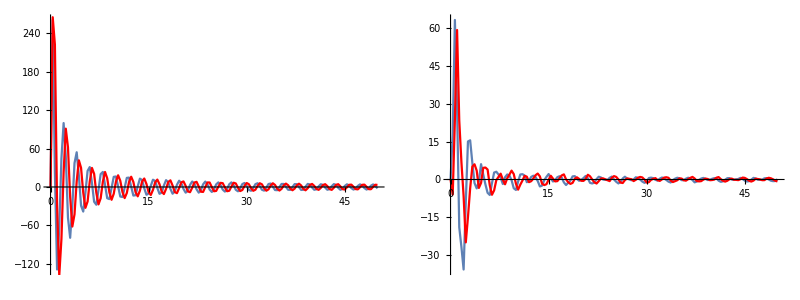

```mathematica
{{Show[
ListLinePlot[{{0}~Join~freqvec/2/Pi,{0}~Join~(Re@test[[1]])}ᵀ,PlotRange->{{0,50},Full},ImageSize->Large],
ListLinePlot[{{0}~Join~freqvec/2/Pi,{0}~Join~(Im@test[[1]] )}ᵀ,PlotRange->Full,PlotStyle->Red]
],
Show[
ListLinePlot[{{0}~Join~freqvec/2/Pi,{0}~Join~(Re@test[[2]])}ᵀ,PlotRange->{{0,50},Full},ImageSize->Large],
ListLinePlot[{{0}~Join~freqvec/2/Pi,{0}~Join~(Im@test[[2]] )}ᵀ,PlotRange->Full,PlotStyle->Red]
]}}//TableForm
```

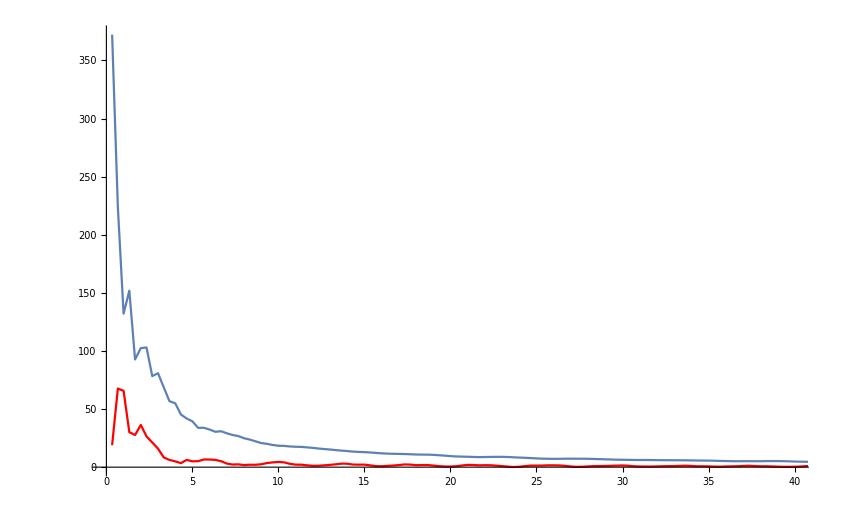

```mathematica
Show[
ListLinePlot[{freqvec/2/Pi,Abs@test[[1]]}ᵀ,PlotRange->{{0,40},Full}],
ListLinePlot[{freqvec/2/Pi,Abs@test[[2]] }ᵀ,PlotRange->Full,PlotStyle->Red]
]
```

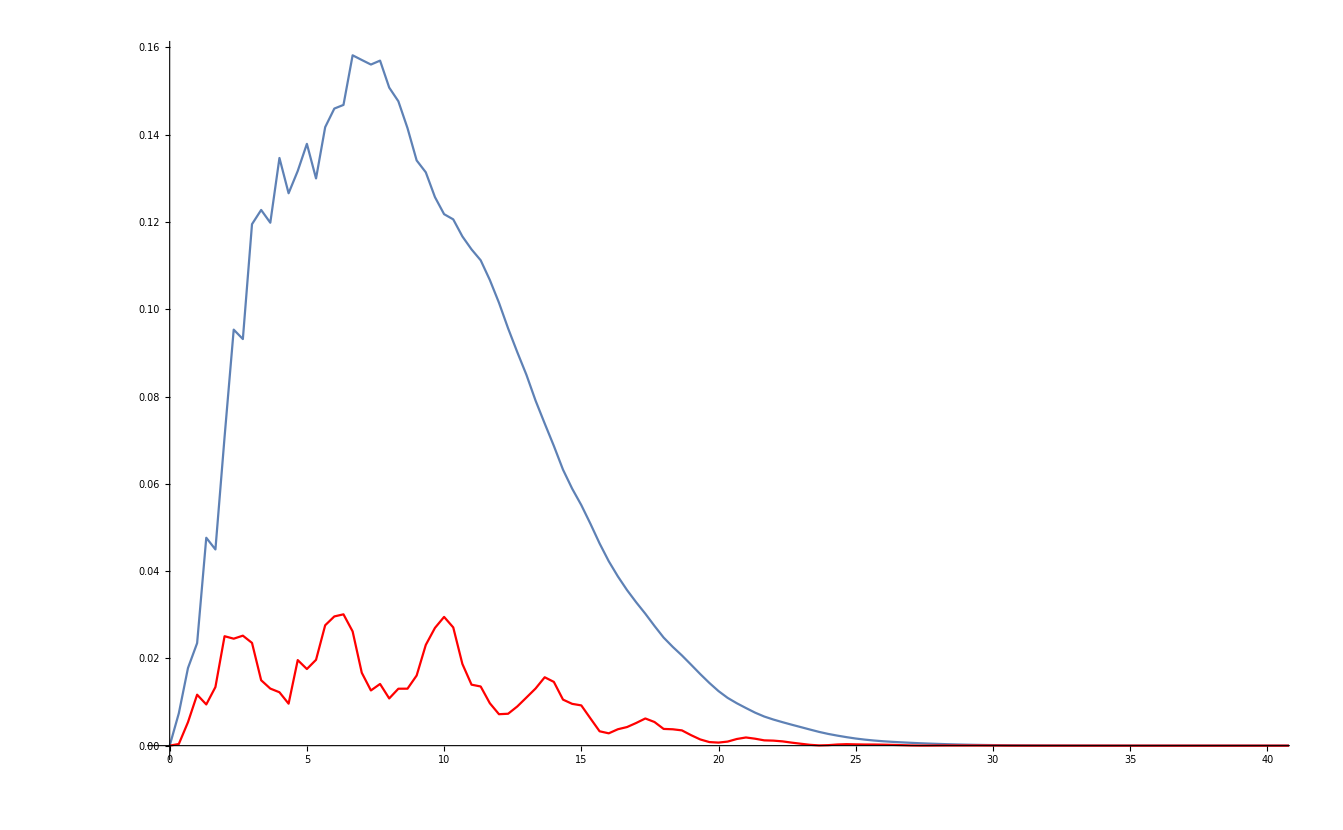

```mathematica
rickerSpectrum[w_,wp_]:=(2 w^2)/(Sqrt[π] wp^3) Exp[-(w^2/wp^2)];

Show[
ListLinePlot[{{0}~Join~freqvec/2/Pi,{0}~Join~(Abs@test[[1]](rickerSpectrum[#,2Pi 10]&/@freqvec))}ᵀ,PlotRange->{{0,40},Full}],
ListLinePlot[{{0}~Join~freqvec/2/Pi,{0}~Join~(Abs@test[[2]] (rickerSpectrum[#,2Pi 10]&/@freqvec))}ᵀ,PlotRange->Full,PlotStyle->Red]
]
```

#### Convert the data to x-t space

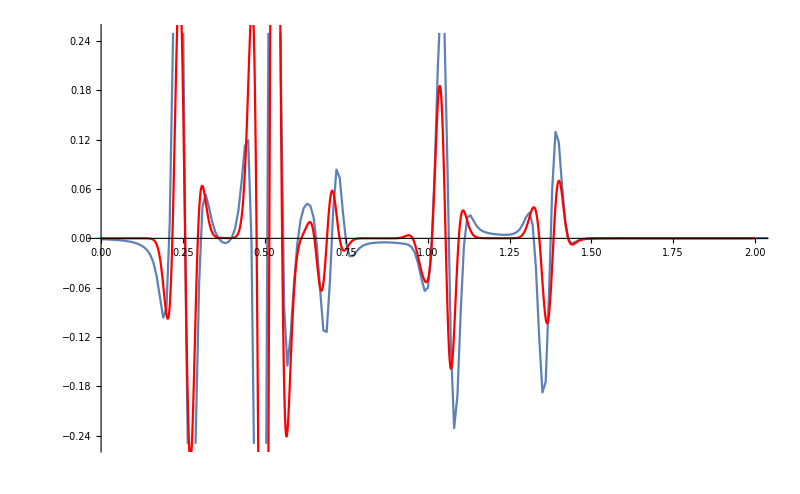

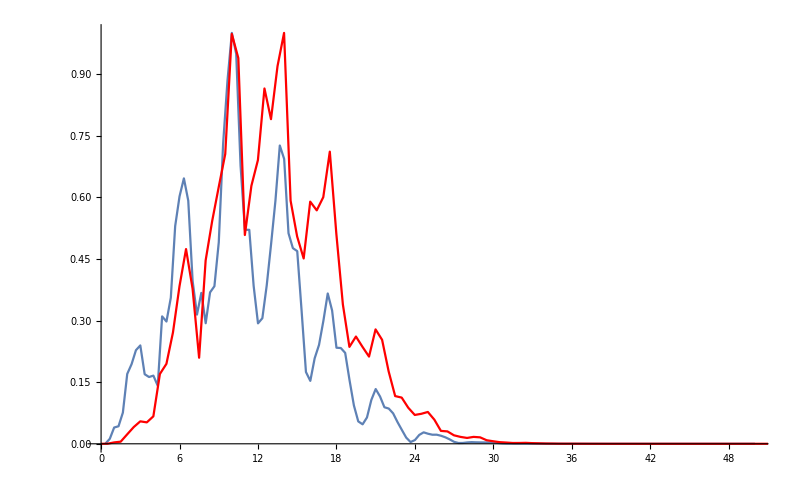

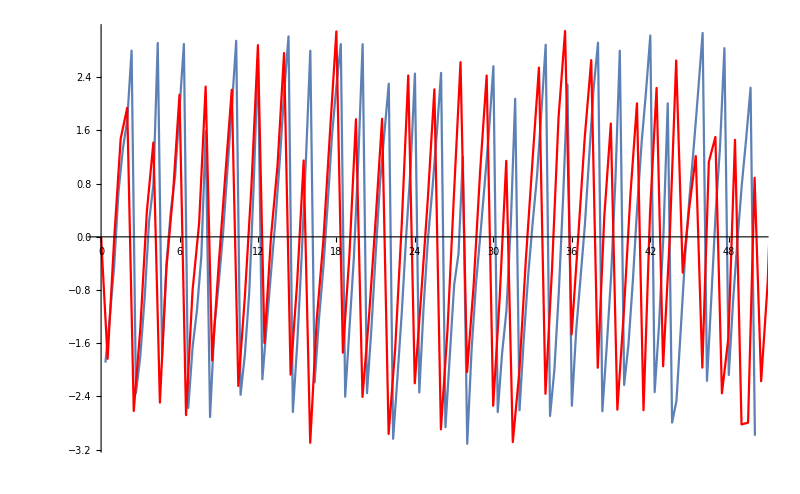

```mathematica
Module[{u=test,ω=freqvec,ωFD,FDu,i=2,int,dispfield,reflSource,fRicker=10,reflTX,t,importFD,FDdispfield,FDω,FDreflSource,FDt,FDreflTX,importFDVTI,reflSourceFD},
(*
r:1; z:2
*)

importFDVTI=BinaryReadList[NotebookDirectory[]<>"FD_VTI","Real32"];
FDu=RotateLeft[{importFDVTI[[2002;;4002]],importFDVTI[[1;;2001]]},{0,141}];
dispfield= u[[i]];
FDdispfield=FDu[[i]];

t=With[{len=Length@ω,df=(ω[[2]]-ω[[1]])/(2Pi)},Range[0,2len]/(df (2len))];FDt=With[{dt=0.001,Nt=2001},Range[0,dt (Nt-1),dt]];

reflSource=-(I ω )^1 dispfield(rickerSpectrum[#,2Pi fRicker]&/@ω);
reflSourceFD=With[{f=Fourier[FDdispfield]},f/Max@Abs@f];
ωFD=With[{len=2001,dt=0.001},2Pi Range[0,(len-1)/2]/(dt (len))];

reflTX=Exp[ωI t]InverseFourier[{0.}~Join~reflSource~Join~Conjugate@Reverse@reflSource];
reflSource=reflSource/Max[Abs@reflSource];
Print[Show[ListLinePlot[{t,(Re@reflTX)/Max[Abs@reflTX]}ᵀ,PlotRange->{{0,2},{-1,1}.25},ImageSize->800],ListLinePlot[{FDt,(Re@FDdispfield)/Max[Abs@FDdispfield]}ᵀ,PlotRange->Full,PlotStyle->Red]]];

Print[Show[
ListLinePlot[{ω/2/Pi,Abs@reflSource}ᵀ,PlotRange->{{0,Max@ω/2/Pi},{0,1}},ImageSize->800],
ListLinePlot[{ωFD/2/Pi,Abs@reflSourceFD[[1;;1001]]}ᵀ,PlotRange->{{0,Max@ω/2/Pi},{0,1}},PlotStyle->Red]]];

Print[Show[
ListLinePlot[{ω/2/Pi,Arg@reflSource}ᵀ,PlotRange->{{0,Max@ω/2/Pi},Full},ImageSize->800],
ListLinePlot[{ωFD/2/Pi,Arg@reflSourceFD[[1;;1001]]}ᵀ,PlotRange->{{0,Max@ω/2/Pi},Full},PlotStyle->Red]]];

]
```

## ISO Comparison with FD

#### Compute data in x-ω space

```mathematica
<<ThinLayer`
```

```mathematica
setlayer[]:=Module[{},
tlSetLayer[1,tlCijFromThomsen[2.0002,1.0002,0,0,2.0002]];
tlSetLayer[2,tlCijFromThomsen[3.0002,1.5002,0,0,3.0002]];
]
```

```mathematica
setlayer[]
```

```mathematica
BZV=Uncompress@Import[NotebookDirectory[]<>"BesselZeros.mc","String"];
```

```mathematica
Module[
{r=.3,layers,zs,zr,overburden,model,pcrit,dList,integrandp,toHTp,HTvec,Nfreq,Np,deltafreq,maxfreq,ωList,toHTk,ur,uz,timingHT,timingPMAX,timingBessel,dp,pI,T,HW,BV},

(* ==== MODEL PARAMETERS ====*)
zs=.3;
zr=.4;
overburden=1;
layers={2};
model={overburden,Sequence@@layers};
dList={0,0};

pcrit=Flatten[N@(({#[[1]],#[[4]]}/(#[[-1]]))^(-1/2))&/@tlGetStiffness[model]];

Nfreq=100;
maxfreq=50.;
deltafreq=maxfreq/Nfreq;
ωList=2Pi Range[deltafreq,maxfreq,deltafreq]//N;
freqvec=ωList;

ωI=Log[10.]deltafreq/5;


(*===DHT===*)

uz[p_,ω_]:=tlResponse[model,dList,p( ω-I ωI)/√(ω^2+ωI^2),ω+I ωI,zs,zr][[1]];
ur[p_,ω_]:=tlResponse[model,dList,p( ω-I ωI)/√(ω^2+ωI^2),ω+I ωI,zs,zr][[2]];

Module[{np=10000,BesselVector,rmax,pmax,BesselTakeUpToN},

BesselVector=BZV[[;;,1;;np]];

BesselTakeUpToN[w_]=Ceiling[Interpolation[{{ωList[[1]],10000},{ωList[[-1]],np}},InterpolationOrder->1][w]];

pmax[ω_]=1.2Max@Abs@pcrit;
rmax[ω_]:=BesselVector[[1,BesselTakeUpToN[ω]]]/ω/pmax[ω];

DistributeDefinitions[ur,uz,BesselVector,rmax,setlayer,ωList,BesselTakeUpToN,r,ωI];
DistributeDefinitions["ThinLayer`"];

timingHT=
AbsoluteTiming[
test=Transpose@ParallelTable[
setlayer[];
BV=BesselVector[[;;,1;;BesselTakeUpToN[ω]]];

u={uz[#,ω]&/@(BV[[1]]/rmax[ω]/ω),ur[#,ω]&/@(BV[[2]]/rmax[ω]/ω)};

{Quiet@tlDHTR[u[[1]],0,r,rmax[ω],BV[[1]]],
Quiet@tlDHTR[u[[2]],1,r,rmax[ω],BV[[2]]]}/ω/ω,{ω,ωList}
];
][[1]];

Print["Time taken to calculate inverse Hankel transform: "<>ToString[timingHT]<>" sec"];
];


(*===DIRECT INTEGRATION===*)
(*Module[{pmax,u,pvec},

(* ==== SEISMIC RESPONSE FUNCTION ====*)
u[p_,ω_]:=tlResponseVforce[model,dList,p,ω+I ωI,zs,zr,r];

pmax[ω_]=1.2Max@Abs@pcrit;
Np=5000;
dp[ω_]=pmax[ω]/Np;


DistributeDefinitions["ThinLayer`"];
DistributeDefinitions[setlayer,u,ωList,ωI,pmax,dp];

freqvec=ωList;
AbsoluteTiming[
test=
Transpose@ParallelTable[

setlayer[];
pvec=#-I#/ω ωI&/@Range[0,pmax[ω],(dp[ω]ω)/(√(ω^2+ωI^2))];
Total[u[#,ω]&/@pvec]

,
{ω,ωList}];
]
]*)
]
```

Time taken to calculate inverse Hankel transform: 2554.9 sec

#### Convert the data to x-t space

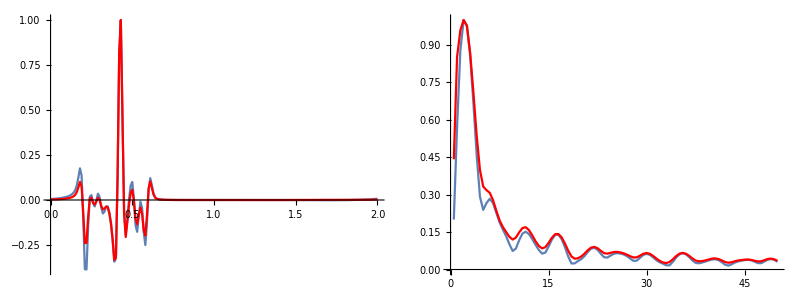

```mathematica
rickerSpectrum[w_,wp_]:=(2 w^2)/(Sqrt[π] wp^3) Exp[-(w^2/wp^2)];

Module[{u=test,ω=freqvec,FDu,i=2,int,dispfield,reflSource,fRicker=15,reflTX,t,importFD,FDdispfield,FDω,FDreflSource,FDt,FDreflTX},
(*
r:1; z:2
*)

importFD=Import[NotebookDirectory[]<>"ivan.txt","Data"];
{FDω,FDu}=Transpose[{#[[1]],{#[[4]]+I#[[5]],#[[2]]+I#[[3]]}}&/@importFD];

dispfield=u[[i]];
FDdispfield=Transpose[FDu][[i]];

t=With[{len=Length@ω,df=(ω[[2]]-ω[[1]])/(2Pi)},Range[0,2len]/(df (2len))];
FDt=With[{len=Length@FDω,df=(FDω[[2]]-FDω[[1]])/(2Pi)},Range[0,2len]/(df (2len))];


reflSource=dispfield(rickerSpectrum[#,2Pi fRicker]&/@ω);
FDreflSource=FDdispfield(rickerSpectrum[#,2Pi fRicker]&/@FDω);


reflTX=Exp[ωI t]InverseFourier[RotateLeft[(Reverse@Conjugate@reflSource)~Join~{0+0. I}~Join~reflSource,Length@ω]];
FDreflTX=InverseFourier[RotateLeft[(Reverse@Conjugate@FDreflSource)~Join~{0+0. I}~Join~FDreflSource,Length@FDω]];

reflSource=reflSource/Max[Abs@reflSource];
FDreflSource=FDreflSource/Max[Abs@FDreflSource];



{{Show[ListLinePlot[{t,(Re@reflTX)/Max[Abs@reflTX]}ᵀ,PlotRange->Full,ImageSize->Large],ListLinePlot[{FDt,(Re@FDreflTX)/Max[Abs@FDreflTX]}ᵀ,PlotRange->Full,PlotStyle->Red]],Show[ListLinePlot[{ω/(2Pi),(Abs@dispfield)/(Max@Abs@dispfield)}ᵀ,PlotRange->Full,ImageSize->Large],ListLinePlot[{FDω/(2Pi),(Abs@FDdispfield)/(Max@Abs@FDdispfield)}ᵀ,PlotRange->Full,PlotStyle->Red]]}}//TableForm


]
```

## Response of fractures

### Model parameters test

```mathematica
<<ThinLayer`
```

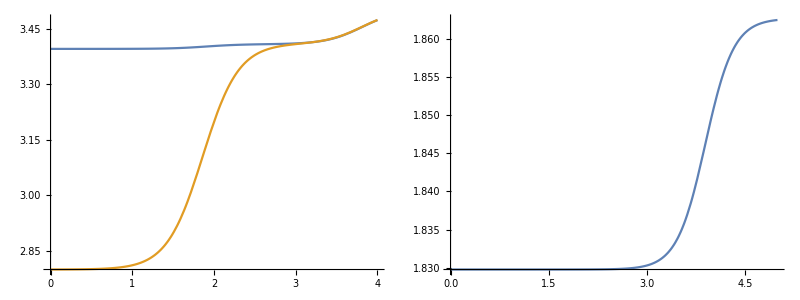

```mathematica
With[{λ=10.6957 ,μ=21.9734 ,ρ=2.15,ϕ=.28,kf=2.4 ,ϵ=0.02,ϵf=0.03,α=10^-5,τ=2 10^-5,lenrat=100},
cij[f_]=tlVTISquirtModuli[ϵ,ϵf,α,τ,2Pi f,lenrat][λ,μ,ρ,ϕ,kf];
Print[{{Plot[Evaluate@Re[{√((#[[1]])/(#[[5]])),√((#[[3]])/(#[[5]]))}&@cij[10^f]],{f,0,4},PlotRange->{Full,Full},ImageSize->Large],Plot[Evaluate@Re[√((#[[4]])/(#[[5]]))&@cij[10^f]],{f,0,5},PlotRange->{Full,Full},ImageSize->Large]}}//TableForm];
]
```

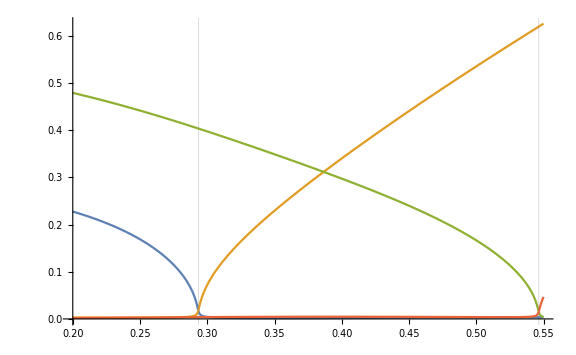

```mathematica
With[{f=10},tlSetLayer[1,Re@#-I Abs@Im@#&@cij[2Pi 100]];
Plot[Evaluate@ReIm@tlQLmatrices[1,p][[1]],{p,0.2,.55},PlotPoints->500,GridLines->{Abs[({#[[1]],#[[4]]}/(#[[-1]]))^(-1/2)&@tlGetStiffness[1]],None},ImageSize->Large]]
```

#### Compute data in x-ω space

```mathematica
<<ThinLayer`
```

```mathematica
BZV=Uncompress@Import[NotebookDirectory[]<>"BesselZeros.mc","String"];
Print["Number of J roots: "<>ToString[Dimensions[BZV][[2]]]];
```

Number of J roots: 30000

```mathematica
computeResponse[Nrep_,Nfreq_,maxfreq_,offsets_,lenrat_,BV_]:=
Module[{zs=.4,zb=.8,D2=.6,layers,overburden,model,dList,integrandp,toHTp,HTvec,deltafreq,ωList,toHTk,HW,uz,ur,pcrit,UzUr,time,ωI,Nb,test,setlayer},
(* ==== MODEL PARAMETERS ====*)
overburden=1;
layers={2}~Join~(Sequence@@@ConstantArray[{3,2},Nrep])~Join~{2};
dList={0}~Join~ConstantArray[D2/(Length@layers-1),Length@layers-1]~Join~{0};
model={overburden,Sequence@@layers};

setlayer[ω_]:=Module[
{λ=10.6957 ,μ=21.9734 ,ρ2=2.15,ϕ=.28,kf=2.4 ,ϵ=0.02,ϵf=0.03,α=10^-5,τ=2 10^-5,cij,vp1=2.8,vs1=1.5,ρ1=2.4,vp2=2.9,vs2=1.7},
cij=tlVTISquirtModuli[ϵ,ϵf,α,τ,ω,lenrat][λ,μ,ρ2,ϕ,kf];
tlSetLayer[1,tlCijFromThomsen[vp1,vs1,0,0,ρ1]];
tlSetLayer[2,Re@#-I Abs@Im@#&@cij];
tlSetLayer[3,tlCijFromThomsen[vp2,vs2,0,0,ρ1]];
tlSetLayer[4,2(Re@#-I Abs@Im@#&@cij)];
];

setlayer[0];
pcrit=Flatten[N@(({#[[1]],#[[4]]}/(#[[-1]]))^(-1/2))&/@tlGetStiffness[DeleteDuplicates@model]];
deltafreq=maxfreq/Nfreq;
ωList=2Pi Range[deltafreq,maxfreq,deltafreq]//N;
ωI=Log[10.]deltafreq/5;

HW[p_]:=Module[{p1=0,p2=0,p3=1.05Max@Abs@pcrit,p4=1.1Max@Abs@pcrit},
Piecewise[{{1/2(1+Cos[Pi (p2-p)/(p2-p1)]),p≥p1&&p2≥p},{1,p>p2&&p3>p},{1/2(1+Cos[Pi (p-p3)/(p4-p3)]),p≥p3&&p4≥p}}]
];

uz[p_,ω_]:=HW[p]tlResponseVforce[model,dList,p( ω-I ωI)/ω,ω+I ωI,zs,zb][[1]];
ur[p_,ω_]:=HW[p]tlResponseVforce[model,dList,p( ω-I ωI)/ω,ω+I ωI,zs,zb][[2]];

Nb=Dimensions[BV][[2]];

Module[{BesselTakeUpToN,pmax,rmax},
BesselTakeUpToN[w_]=Ceiling[Interpolation[{{ωList[[1]],Round[Nb/3]},{ωList[[-1]],Nb}},InterpolationOrder->1][w]];

pmax[ω_]=1.1Max@Abs@pcrit;
rmax[ω_]:=BV[[1,BesselTakeUpToN[ω]]]/ω/pmax[ω];

DistributeDefinitions["ThinLayer`"];
DistributeDefinitions[uz,ur,pmax,ωList,offsets,setlayer,rmax,BesselTakeUpToN];

(*===IDHT===*)
time=AbsoluteTiming[
test=ParallelTable[
Module[{BVω=BV[[;;,1;;BesselTakeUpToN[ω]]],u},
setlayer[ω];

u={
uz[#,ω]&/@(BVω[[1]]/rmax[ω]/ω),ur[#,ω]&/@(BVω[[2]]/rmax[ω]/ω)
};

{Quiet@tlDHTR[u[[1]],0,offsets,rmax[ω],BVω[[1]]],
Quiet@tlDHTR[u[[2]],1,offsets,rmax[ω],BVω[[2]]]}]/ω^2
,{ω,ωList},DistributedContexts->"ThinLayer`Private`"
];
][[1]];

Print["It took me "<>ToString[Round[time/60]]<>" minutes"];
{ωList,test,ωI}
]

]
```

#### Computation

```mathematica
(*computeResponse[Nrep_,Nfreq_,maxfreq_,offsets_,lenrat_,BV_]*)
```

```mathematica
x=Range[.1,2,.01];
```

```mathematica
{freqvec,dataL100,ωI}=computeResponse[0,800,150,x,100,BZV[[;;,1;;20000]]];
```

It took me 506 minutes

```mathematica
(*Export[NotebookDirectory[]<>"IHTgatherl100N0t3.mc",Compress[{freqvec,x,ωI,dataL100}],"String"]*)
```

C:\Users\yuriyi\Dropbox\Study_etc\NTNU\Anisotropy\Mathematica\PETROMAKS\PM2-codes\numerics\IHTgatherl100N0t3.mc

```mathematica
{freqvec,dataL200,ωI}=computeResponse[0,800,150,x,200,BZV[[;;,1;;20000]]];
```

It took me 511 minutes

```mathematica
(*Export[NotebookDirectory[]<>"IHTgatherl200N0t3.mc",Compress[{freqvec,x,ωI,dataL200}],"String"]*)
```

C:\Users\yuriyi\Dropbox\Study_etc\NTNU\Anisotropy\Mathematica\PETROMAKS\PM2-codes\numerics\IHTgatherl200N0t3.mc

```mathematica
(*{freqvect1,x1,ωIt1,dataL100t1}=Uncompress@Import[NotebookDirectory[]<>"IHTgatherl100N0.mc"];
{freqvect1,x1,ωIt1,dataL200t1}=Uncompress@Import[NotebookDirectory[]<>"IHTgatherl200N0.mc"];*)
```

```mathematica
{freqvec,x,ωI,l100}=Uncompress@Import[NotebookDirectory[]<>"IHTgatherl100N0t3.mc"];
{freqvec,x,ωI,l200}=Uncompress@Import[NotebookDirectory[]<>"IHTgatherl200N0t3.mc"];
```

```mathematica
{freqvec,dataTest,ωI}=computeResponse[0,150,50,x,100,BZV[[;;,1;;10000]]];
```

It took me 44 minutes

#### Plotting

```mathematica
ClearAll[plot]
rickerSpectrum[w_,wp_]:=(2 w^2)/(Sqrt[π] wp^3) Exp[-(w^2/wp^2)];
plot[u_,ω_,offsets_,ampl_,ωI_,model_,dlist_,output_:0,fRicker_:25]:=Module[{dispfield,reflSource,reflTX,t,mm},

dispfield=u;
t=With[{len=Length@ω,df=(ω[[2]]-ω[[1]])/(2Pi)},Range[0,2len]/(df (2len))];

reflSource= dispfield(rickerSpectrum[#,2Pi fRicker]&/@ω);
reflTX=Table[
Exp[ωI t]InverseFourier[{0+0. I}~Join~(reflSource[[;;,i]])~Join~(Reverse@Conjugate@reflSource[[;;,i]])],{i,1,Dimensions[reflSource][[2]]}];

If[Head@output==Symbol,Print["{data, t} written to "<>ToString[output]];output={reflTX,t};];
reflTX=ampl Reverse[(Re@reflTX)/(Max@Abs@reflTX),2]ᵀ;
mm=MinMax@reflTX;Print[mm];
Module[{pr={0,2},TToptns,is=1000,tt=tlTravelTimes[model,dlist,#,.4,.8]&,lbls={{"t, s",None},{None,"x, km"}},cfg=Blend[{Black,White},(#-mm[[1]])/2]&,cfrb=Blend[{Blue,White,Red},(#+1)/2]&,colors={Cyan,Black,Green,Orange,Magenta}},
TToptns={AspectRatio->1,Frame->True,FrameTicks->{{Range[0,Max@t,.5],None},{None,Range[0,Max@offsets,.25]}},ScalingFunctions->{Identity,"Reverse"},PlotRange->{MinMax@offsets,-pr},ImageSize->is,FrameTicksStyle->Opacity[0],FrameLabel->lbls,LabelStyle->Directive[Opacity[0],FontSize->15,Bold,Black],FrameStyle->Opacity[0]};

Print[

Overlay[{
ArrayPlot[reflTX,AspectRatio->1,Frame->True,FrameLabel->RotateRight@lbls,LabelStyle->Directive[FontSize->15,Bold,Black],DataReversed->{True,False},DataRange->{MinMax@(offsets),MinMax@t},FrameTicks->{{Range[0,Max@t,.5],None},{None,Range[0,Max@offsets,.25]}},PlotRange->{MinMax@(offsets),Max@t-Reverse@pr,Full},ImageSize->is,ColorFunction->cfrb,ColorFunctionScaling->False,PlotLegends->Placed[LineLegend[Directive[Thick,#]&/@colors,{"P, S","PP","SS","PS","SP"},LegendLayout->"Row"],Below]],
ParametricPlot[Evaluate@tt[p][[2]],{p,0,1},PlotStyle->Directive[Dashed,Opacity[0],First@colors],#]&@TToptns,
Sequence@@Table[
ParametricPlot[Evaluate@tt[p][[1]][[i]],{p,0,1},PlotStyle->Directive[Dashed,Thick,colors[[i+1]]],#]&@TToptns,{i,1,4}
]
}]
];
];

]
```

{-16.8208,30.}

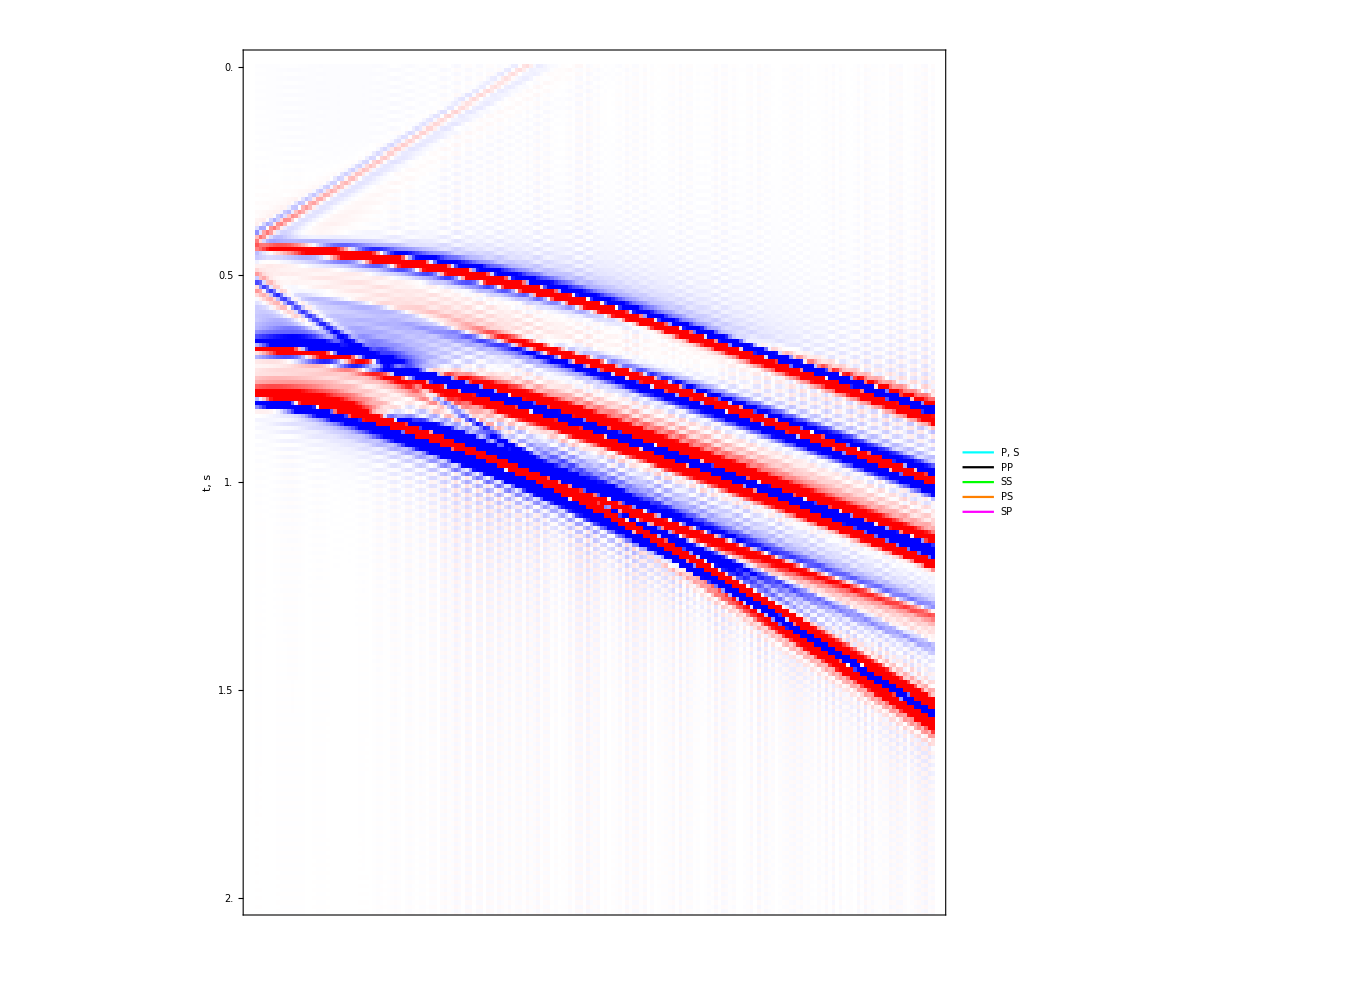
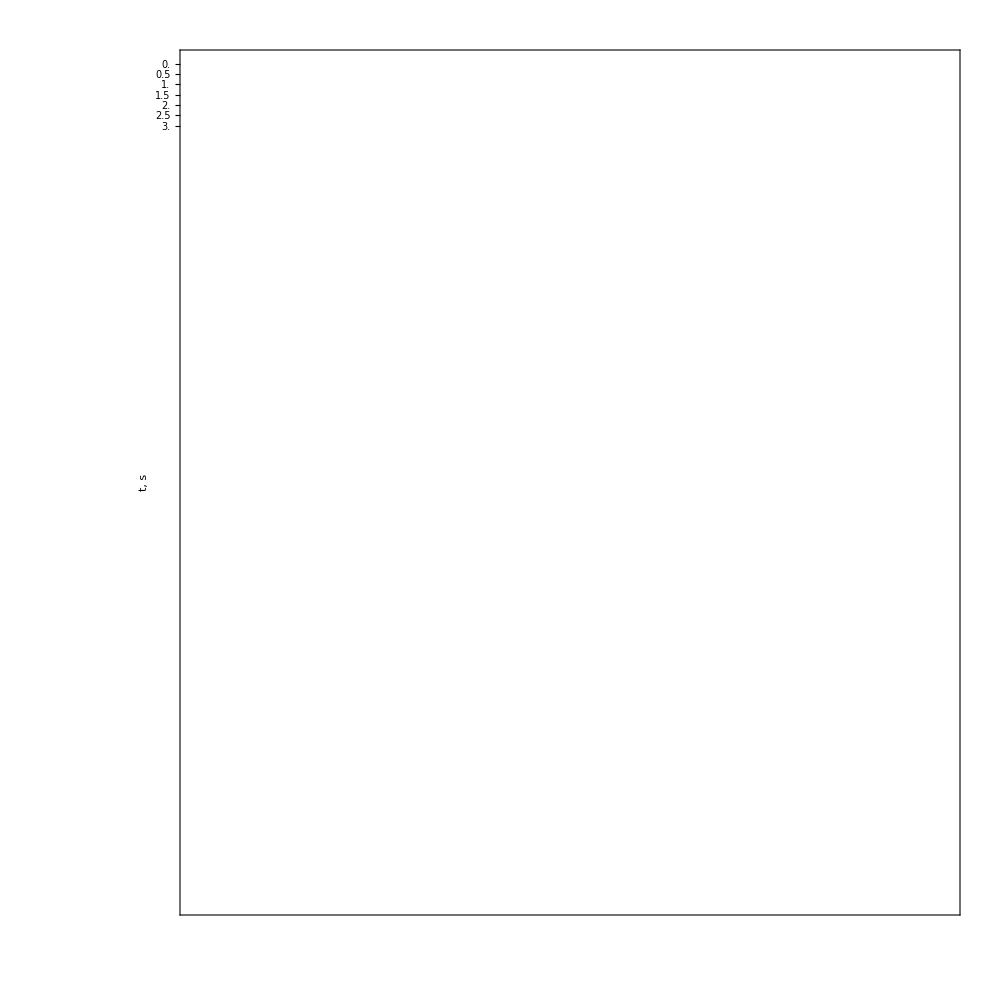
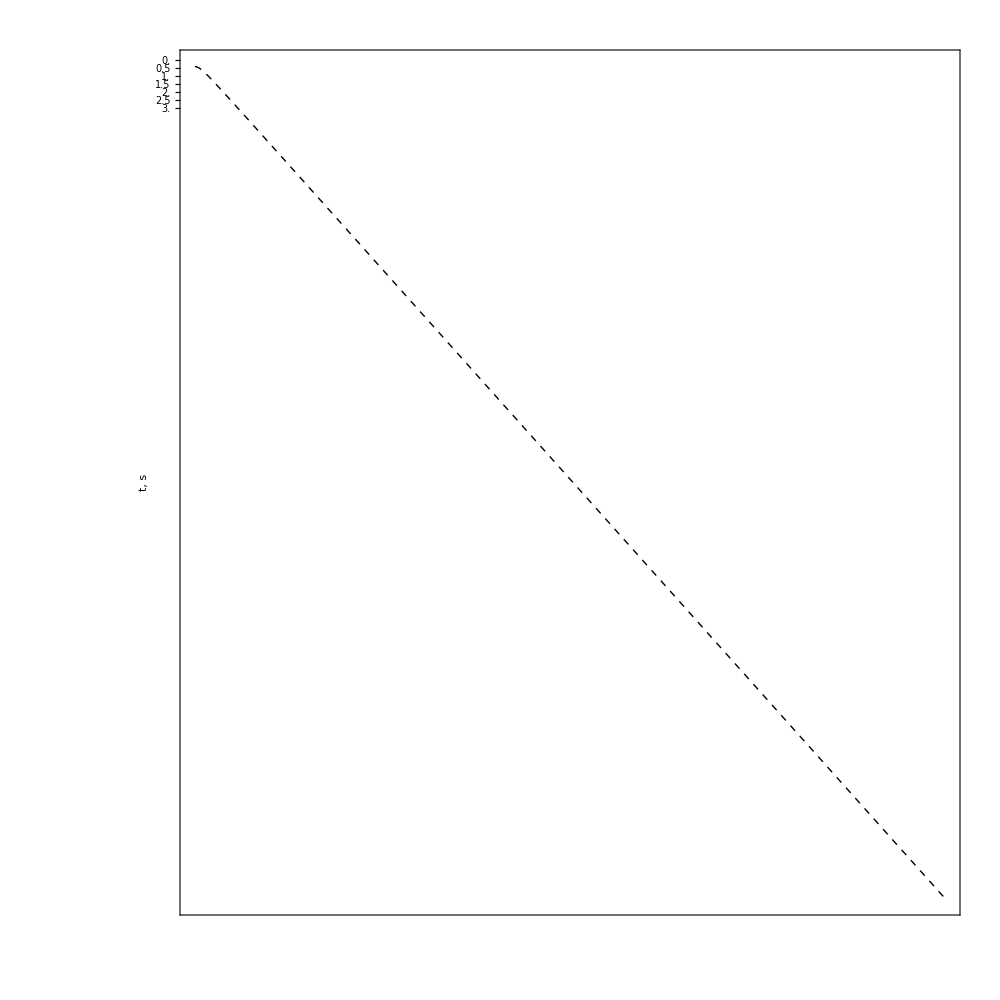
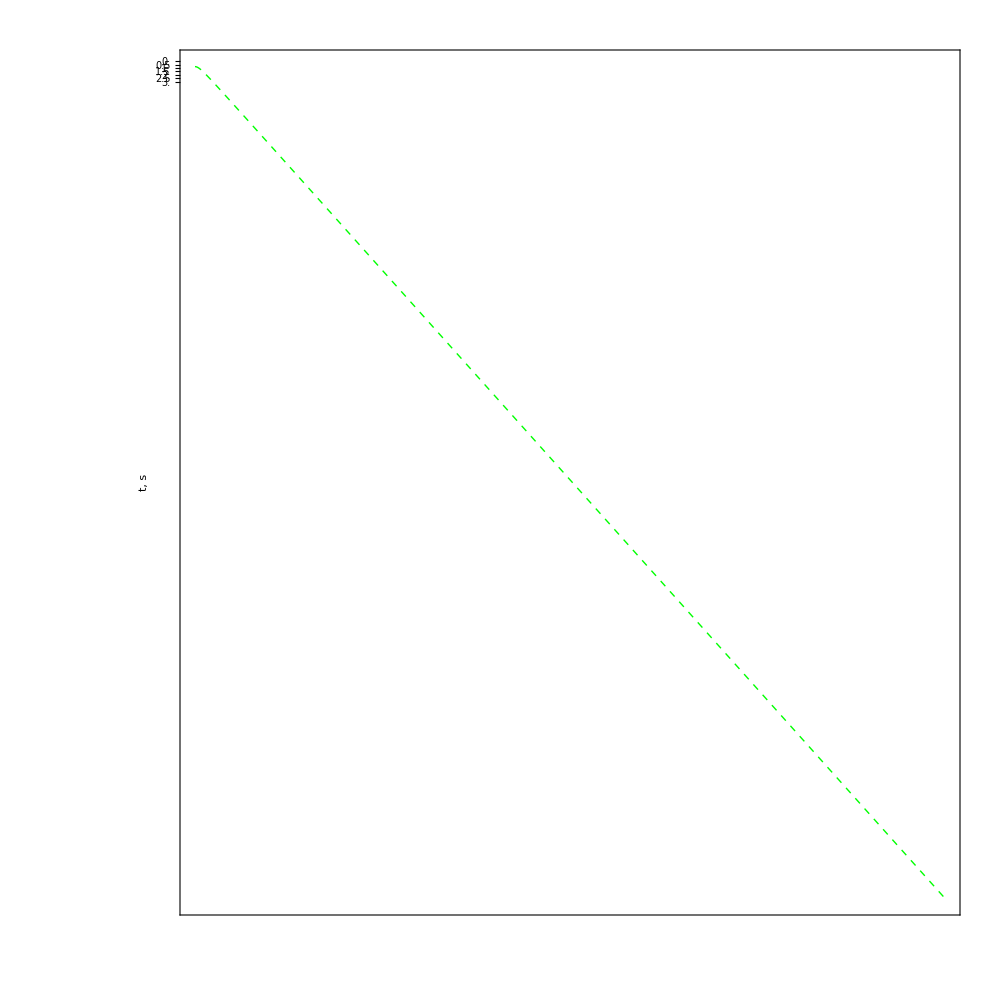
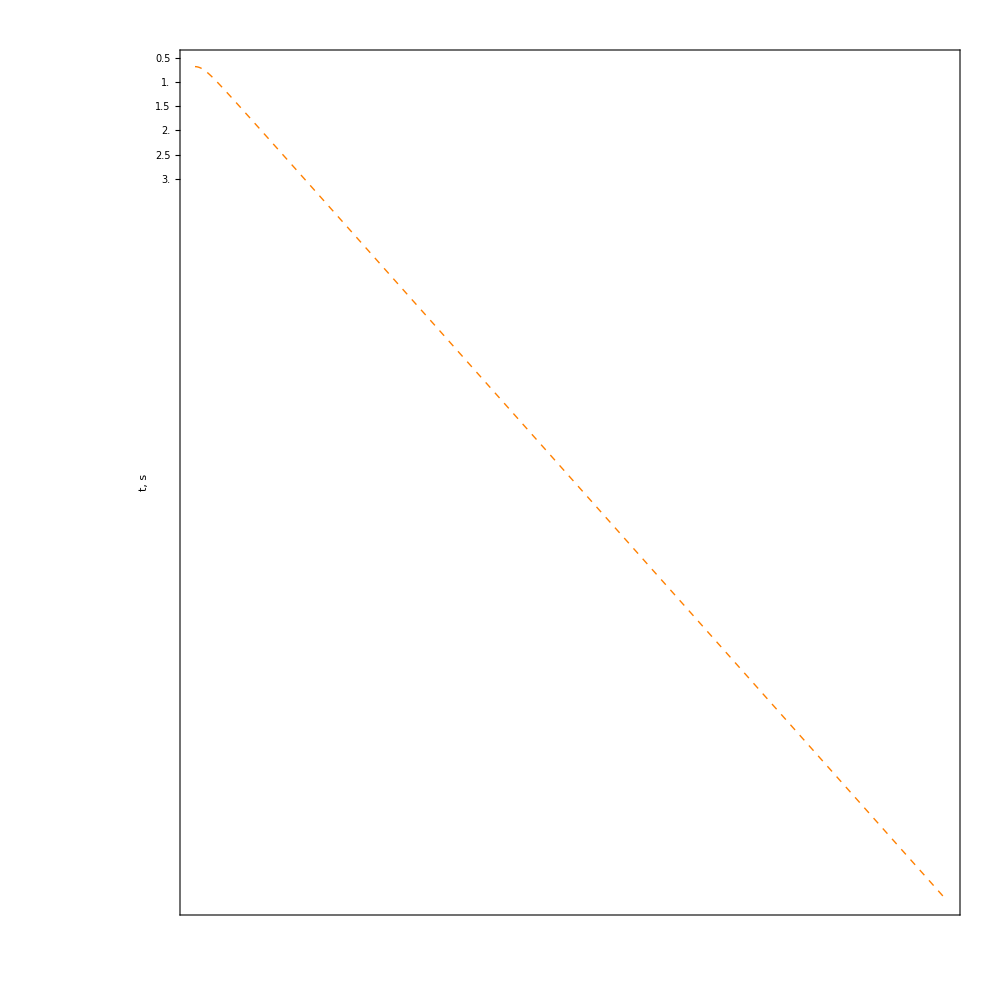
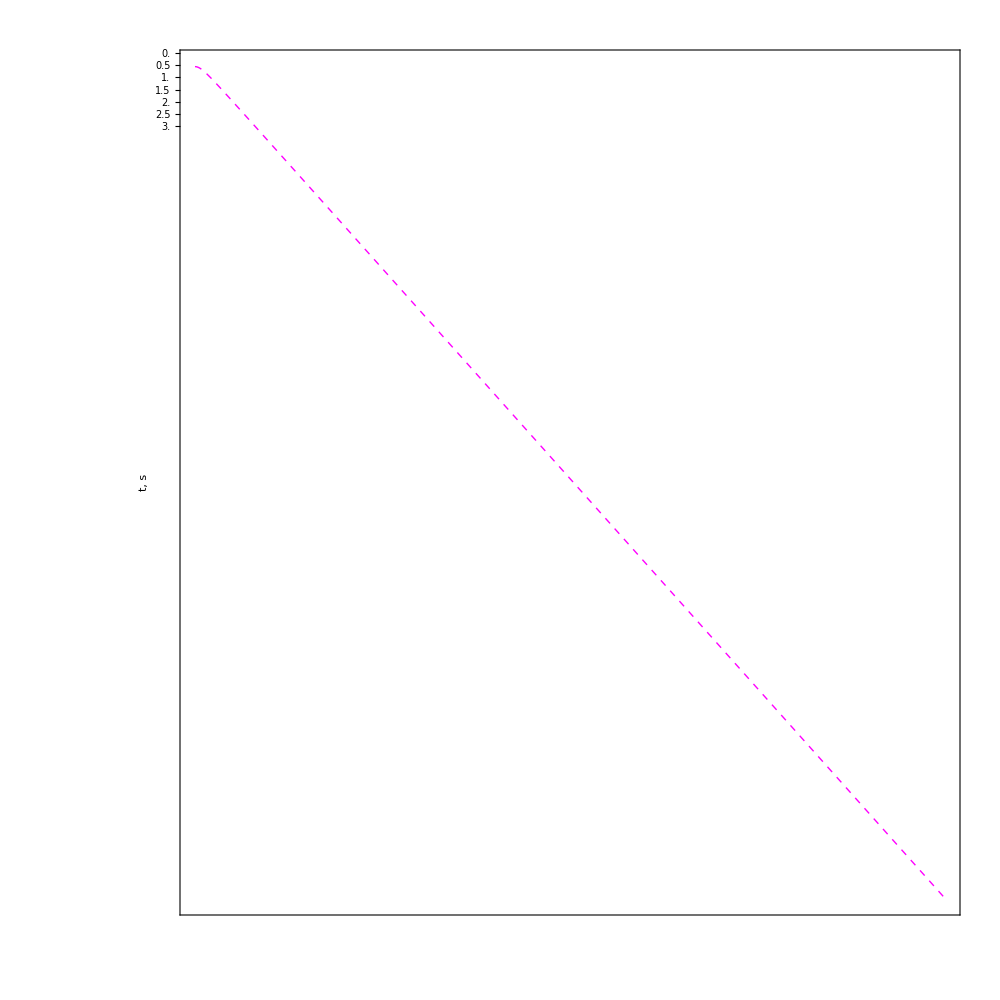

```mathematica
plot[dataTest[[;;,2,;;]],freqvec,x,30,ωI,{1},{0}]
```

```mathematica
ClearAll[plotdiff]
plotdiff[delta_,offsets_,t_,ampl_]:=Module[{reflTX,mm},
reflTX=ampl Reverse[ (Re@delta)/(Max@Abs@delta),2]ᵀ;
mm=MinMax@reflTX;
Module[{pr={0,2},TToptns,is=1000,tt=tlTravelTimes[{1,2},{0, .6},#,.4,.8]&,lbls={{"t, s",None},{None,"x, km"}},cfg=Blend[{Black,White},(#-mm[[1]])/2]&,cfrb=Blend[{Blue,White,Red},(#+1)/2]&,colors={Cyan,Black,Green,Orange,Magenta}},
TToptns={AspectRatio->1,Frame->True,FrameTicks->{{Range[0,Max@t,.5],None},{None,Range[0,Max@offsets,.25]}},ScalingFunctions->{Identity,"Reverse"},PlotRange->{MinMax@offsets,-pr},ImageSize->is,FrameTicksStyle->Opacity[0],FrameLabel->lbls,LabelStyle->Directive[Opacity[0],FontSize->15,Bold,Black],FrameStyle->Opacity[0]};

Print[

Overlay[{
ArrayPlot[reflTX,AspectRatio->1,Frame->True,FrameLabel->RotateRight@lbls,LabelStyle->Directive[FontSize->15,Bold,Black],DataReversed->{True,False},DataRange->{MinMax@(offsets),MinMax@t},FrameTicks->{{Range[0,Max@t,.5],None},{None,Range[0,Max@offsets,.25]}},PlotRange->{MinMax@(offsets),Max@t-Reverse@pr,Full},ImageSize->is,ColorFunction->cfrb,ColorFunctionScaling->False,PlotLegends->Placed[LineLegend[Directive[Thick,#]&/@colors,{"P, S","PP","SS","PS","SP"},LegendLayout->"Row"],Below]],
ParametricPlot[Evaluate@tt[p][[2]],{p,0,1},PlotStyle->Directive[Dashed,First@colors],#]&@TToptns,
Sequence@@Table[
ParametricPlot[Evaluate@tt[p][[1]][[i]],{p,0,1},PlotStyle->Directive[Dashed,colors[[i+1]]],#]&@TToptns,{i,1,4}
]
}]
];
];

]
```

## Misc., Notes, and comments

#### Interface tests

```mathematica
computeResponseInterface[Nrep_,Nfreq_,maxfreq_,offsets_,lenrat_,BV_]:=
Module[{zs=.4,zb=.8,D2=.6,layers,overburden,model,dList,integrandp,toHTp,HTvec,deltafreq,ωList,toHTk,HW,uz,ur,pcrit,UzUr,time,ωI,Nb,test,setlayer},
(* ==== MODEL PARAMETERS ====*)
overburden=1;
layers={3}~Join~(Sequence@@@ConstantArray[{3,2},Nrep])~Join~{3};
dList={0}~Join~ConstantArray[D2/(Length@layers-1),Length@layers-1]~Join~{0};
model={overburden,Sequence@@layers};

setlayer[ω_]:=Module[
{λ=10.6957 ,μ=21.9734 ,ρ2=2.15,ϕ=.28,kf=2.4 ,ϵ=0.02,ϵf=0.03,α=10^-5,τ=2 10^-5,cij,vp1=2.8,vs1=1.5,ρ1=2.4,vp2=2.9,vs2=1.7},
cij=tlVTISquirtModuli[ϵ,ϵf,α,τ,ω,lenrat][λ,μ,ρ2,ϕ,kf];
tlSetLayer[1,tlCijFromThomsen[vp1,vs1,0,0,ρ1]];
tlSetLayer[2,Re@#-I Abs@Im@#&@cij];
tlSetLayer[3,tlCijFromThomsen[vp2,vs2,0,0,ρ1]];
tlSetLayer[4,2(Re@#-I Abs@Im@#&@cij)];
];

setlayer[0];
pcrit=Flatten[N@(({#[[1]],#[[4]]}/(#[[-1]]))^(-1/2))&/@tlGetStiffness[DeleteDuplicates@model]];
deltafreq=maxfreq/Nfreq;
ωList=2Pi Range[deltafreq,maxfreq,deltafreq]//N;
ωI=Log[10.]deltafreq/5;

HW[p_]:=Module[{p1=0,p2=0,p3=1.05Max@Abs@pcrit,p4=1.1Max@Abs@pcrit},
Piecewise[{{1/2(1+Cos[Pi (p2-p)/(p2-p1)]),p≥p1&&p2≥p},{1,p>p2&&p3>p},{1/2(1+Cos[Pi (p-p3)/(p4-p3)]),p≥p3&&p4≥p}}]
];

uz[p_,ω_]:=HW[p]tlResponseVforce[model,dList,p( ω-I ωI)/ω,ω+I ωI,zs,zb][[1]];
ur[p_,ω_]:=HW[p]tlResponseVforce[model,dList,p( ω-I ωI)/ω,ω+I ωI,zs,zb][[2]];

Nb=Dimensions[BV][[2]];

Module[{BesselTakeUpToN,pmax,rmax},
BesselTakeUpToN[w_]=Ceiling[Interpolation[{{ωList[[1]],Round[Nb/3]},{ωList[[-1]],Nb}},InterpolationOrder->1][w]];

pmax[ω_]:=1.1Max@Re@pcrit;
rmax[ω_]:=BV[[1,BesselTakeUpToN[ω]]]/ω/pmax[ω];

DistributeDefinitions["ThinLayer`"];
DistributeDefinitions[uz,ur,pmax,ωList,offsets,setlayer,rmax,BesselTakeUpToN];

(*===IDHT===*)
time=AbsoluteTiming[
test=ParallelTable[
Module[{BVω=BV[[;;,1;;BesselTakeUpToN[ω]]],u},
setlayer[ω];

u={
uz[#,ω]&/@(BVω[[1]]/rmax[ω]/ω),ur[#,ω]&/@(BVω[[2]]/rmax[ω]/ω)
};

{Quiet@tlDHTR[u[[1]],0,offsets,rmax[ω],BVω[[1]]],
Quiet@tlDHTR[u[[2]],1,offsets,rmax[ω],BVω[[2]]]}]/ω^2
,{ω,ωList},DistributedContexts->"ThinLayer`Private`"
];
][[1]];

Print["It took me "<>ToString[Round[time/60]]<>" minutes"];
{ωList,test,ωI}
]

]
```

```mathematica
x=Range[.1,2,.01];
```

```mathematica
{freqvec,dataTest2,ωI}=computeResponseInterface[0,150,50,x,100,BZV[[;;,1;;10000]]];
```

It took me 44 minutes

{-3.62747,10.}

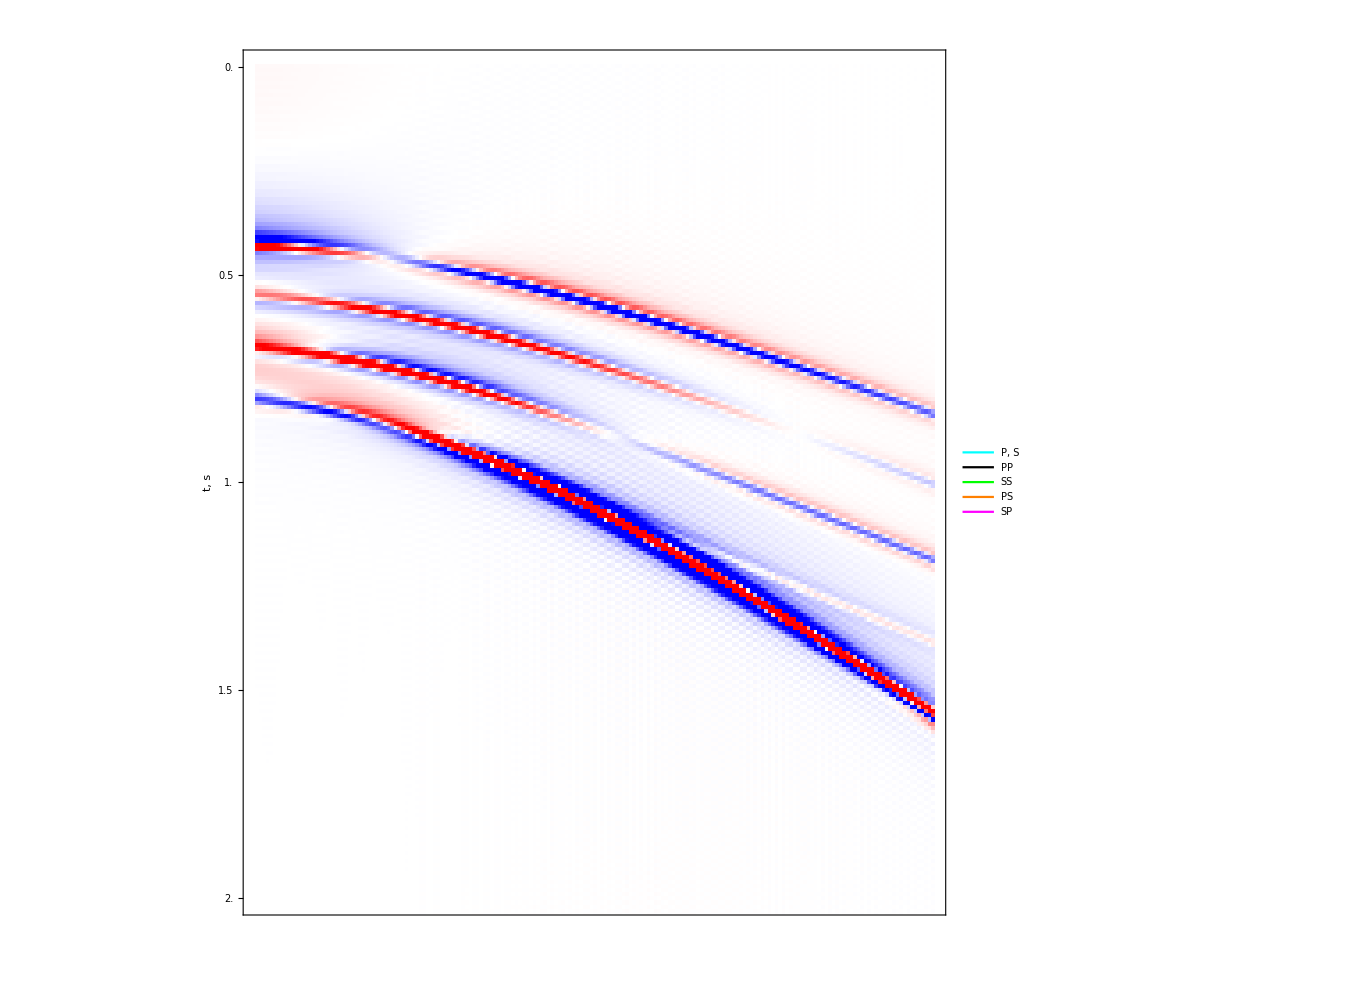
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
plot[dataTest2[[;;,1,;;]],freqvec,x,10,ωI,{1},{0}]
```

```mathematica
computeResponseInterface2[Nrep_,Nfreq_,maxfreq_,offsets_,lenrat_,BV_]:=
Module[{zs=.4,zb=.8,D2=.6,layers,overburden,model,dList,integrandp,toHTp,HTvec,deltafreq,ωList,toHTk,HW,uz,ur,pcrit,UzUr,time,ωI,Nb,test,setlayer},
(* ==== MODEL PARAMETERS ====*)
overburden=2;
layers={4}~Join~(Sequence@@@ConstantArray[{3,2},Nrep])~Join~{4};
dList={0}~Join~ConstantArray[D2/(Length@layers-1),Length@layers-1]~Join~{0};
model={overburden,Sequence@@layers};

setlayer[ω_]:=Module[
{λ=10.6957 ,μ=21.9734 ,ρ2=2.15,ϕ=.28,kf=2.4 ,ϵ=0.02,ϵf=0.03,α=10^-5,τ=2 10^-5,cij1,cij2,vp1=2.8,vs1=1.5,ρ1=2.4,vp2=2.9,vs2=1.7},
cij1=tlVTISquirtModuli[ϵ,ϵf,α,τ,ω,lenrat][λ,μ,ρ2,ϕ,kf];
cij2=tlVTISquirtModuli[ϵ,ϵf,α,τ,ω,2lenrat][λ,μ,ρ2,ϕ,kf];
tlSetLayer[1,tlCijFromThomsen[vp1,vs1,0,0,ρ1]];
tlSetLayer[2,Re@#-I Abs@Im@#&@cij1];
tlSetLayer[3,tlCijFromThomsen[vp2,vs2,0,0,ρ1]];
tlSetLayer[4,Re@#-I Abs@Im@#&@cij2];
];

setlayer[0];
pcrit=Flatten[N@(({#[[1]],#[[4]]}/(#[[-1]]))^(-1/2))&/@tlGetStiffness[DeleteDuplicates@model]];
deltafreq=maxfreq/Nfreq;
ωList=2Pi Range[deltafreq,maxfreq,deltafreq]//N;
ωI=Log[10.]deltafreq/5;

HW[p_]:=Module[{p1=0,p2=0,p3=1.05Max@Abs@pcrit,p4=1.1Max@Abs@pcrit},
Piecewise[{{1/2(1+Cos[Pi (p2-p)/(p2-p1)]),p≥p1&&p2≥p},{1,p>p2&&p3>p},{1/2(1+Cos[Pi (p-p3)/(p4-p3)]),p≥p3&&p4≥p}}]
];

uz[p_,ω_]:=HW[p]tlResponseVforce[model,dList,p( ω-I ωI)/ω,ω+I ωI,zs,zb][[1]];
ur[p_,ω_]:=HW[p]tlResponseVforce[model,dList,p( ω-I ωI)/ω,ω+I ωI,zs,zb][[2]];

Nb=Dimensions[BV][[2]];

Module[{BesselTakeUpToN,pmax,rmax},
BesselTakeUpToN[w_]=Ceiling[Interpolation[{{ωList[[1]],Round[Nb/3]},{ωList[[-1]],Nb}},InterpolationOrder->1][w]];

pmax[ω_]:=1.1Max@Re@pcrit;
rmax[ω_]:=BV[[1,BesselTakeUpToN[ω]]]/ω/pmax[ω];

DistributeDefinitions["ThinLayer`"];
DistributeDefinitions[uz,ur,pmax,ωList,offsets,setlayer,rmax,BesselTakeUpToN];

(*===IDHT===*)
time=AbsoluteTiming[
test=ParallelTable[
Module[{BVω=BV[[;;,1;;BesselTakeUpToN[ω]]],u},
setlayer[ω];

u={
uz[#,ω]&/@(BVω[[1]]/rmax[ω]/ω),ur[#,ω]&/@(BVω[[2]]/rmax[ω]/ω)
};

{Quiet@tlDHTR[u[[1]],0,offsets,rmax[ω],BVω[[1]]],
Quiet@tlDHTR[u[[2]],1,offsets,rmax[ω],BVω[[2]]]}]/ω^2
,{ω,ωList},DistributedContexts->"ThinLayer`Private`"
];
][[1]];

Print["It took me "<>ToString[Round[time/60]]<>" minutes"];
{ωList,test,ωI}
]

]
```

```mathematica
{freqvec,dataTest3,ωI}=computeResponseInterface2[0,150,50,x,100,BZV[[;;,1;;10000]]];
```

{-4.71011,5.}

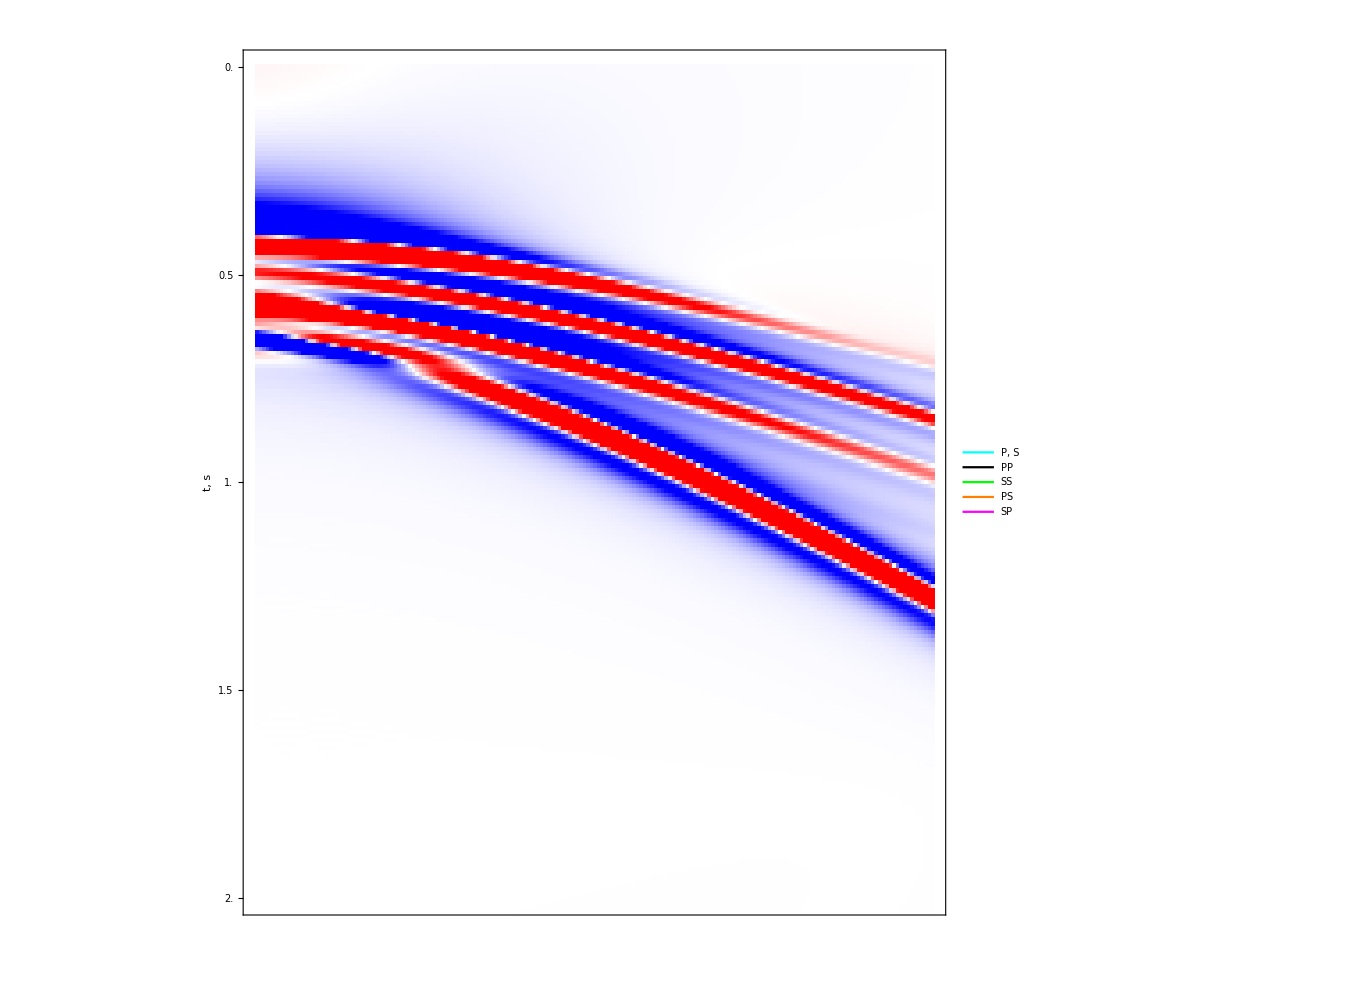
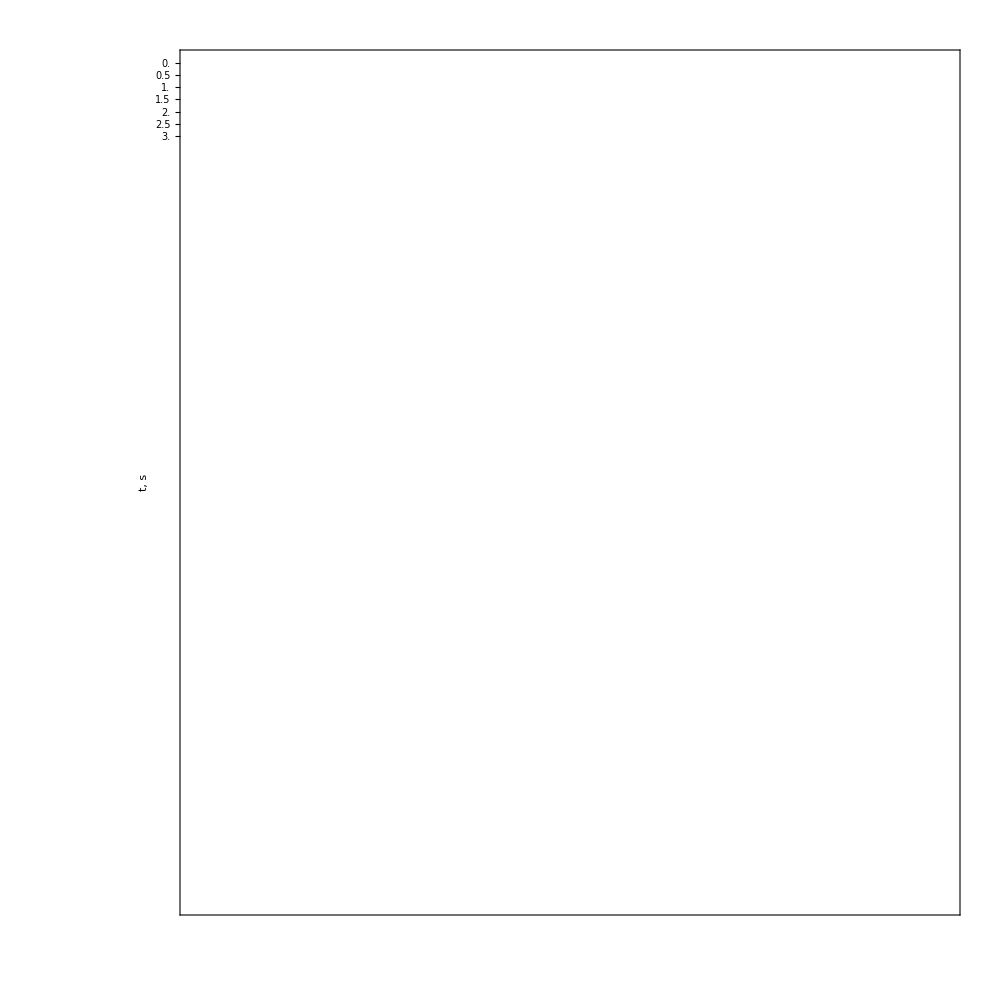
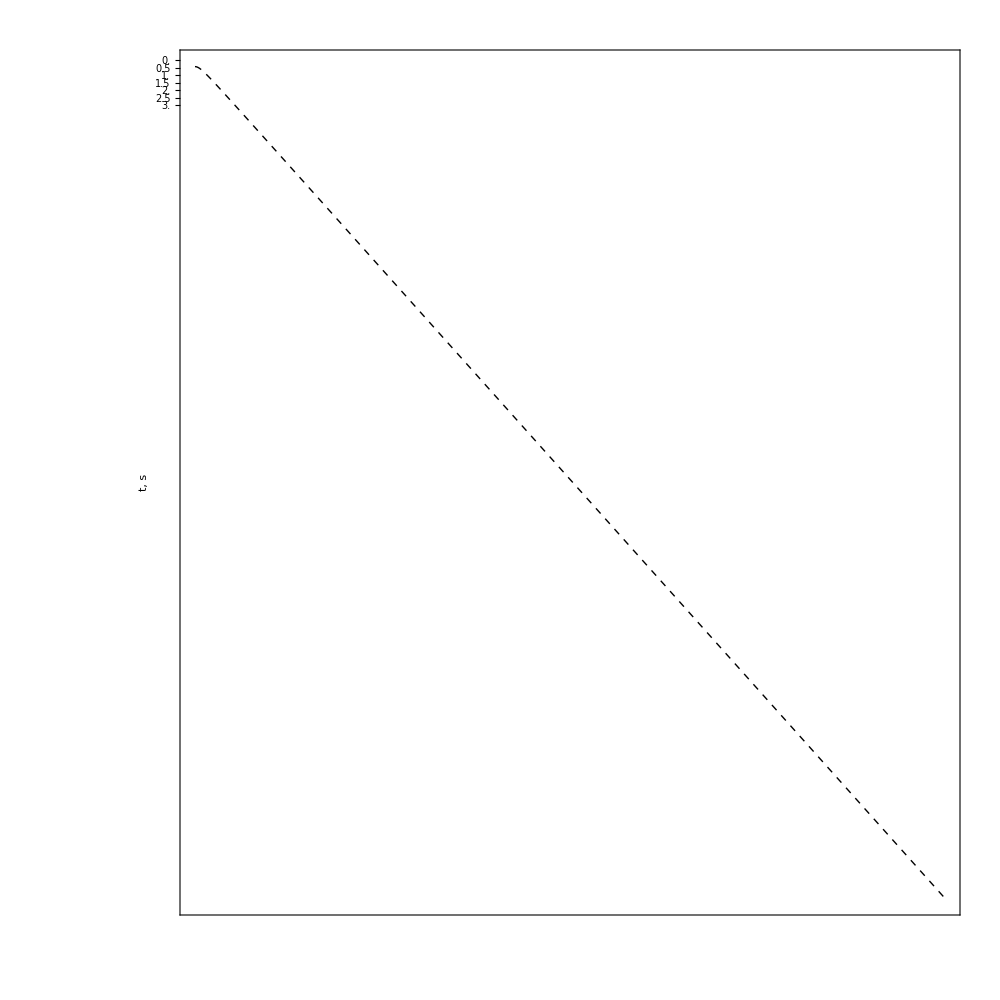
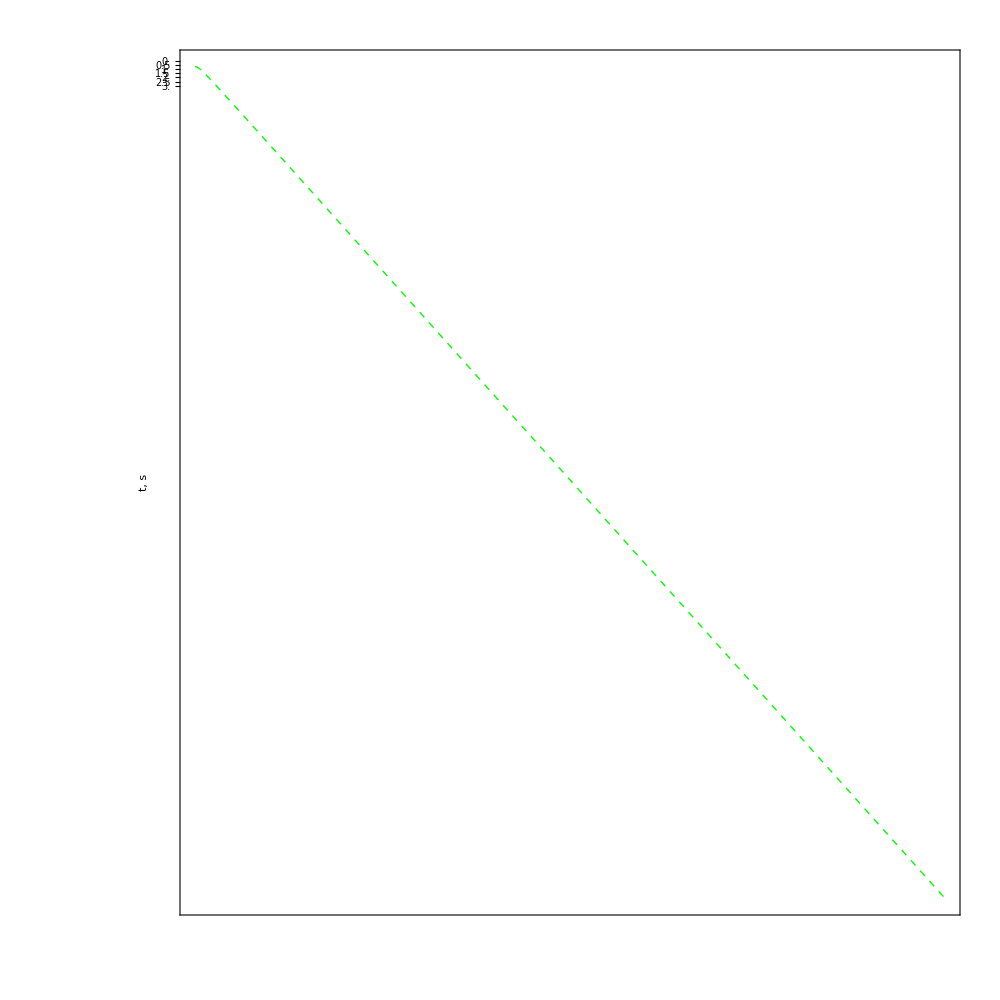
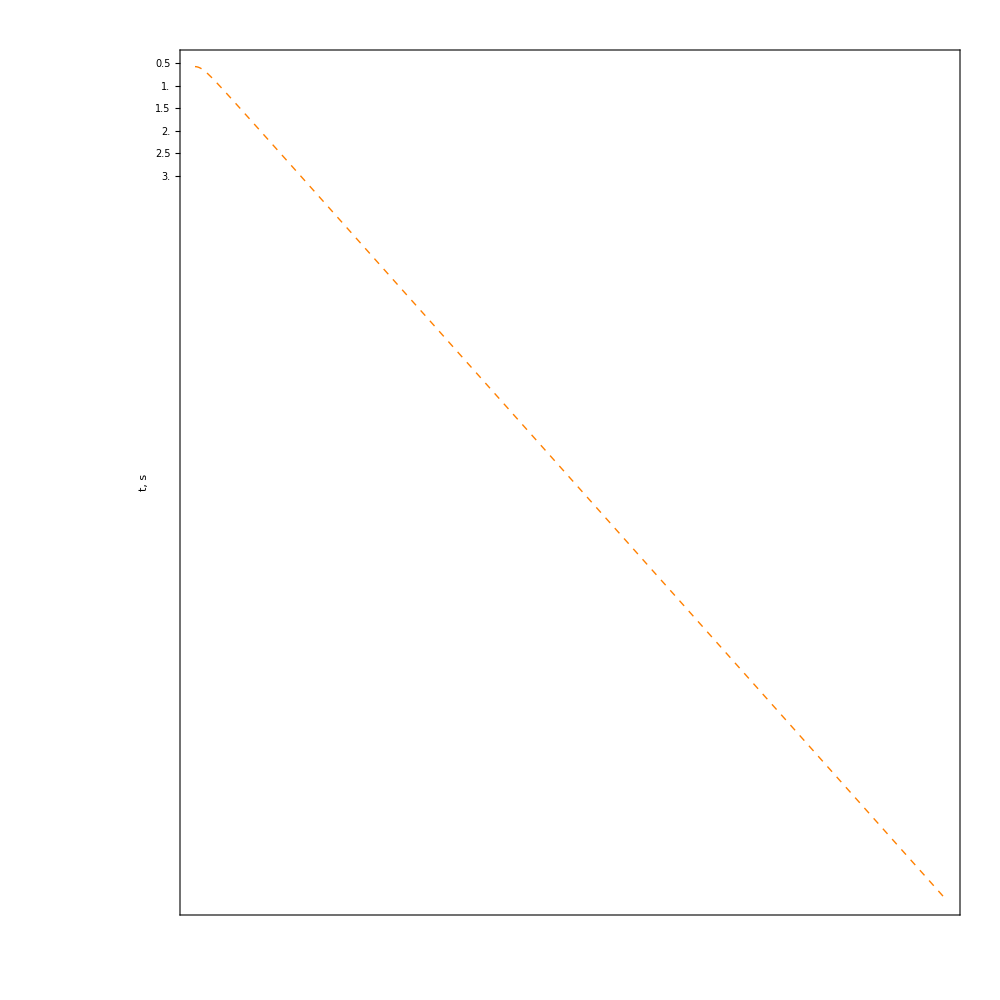
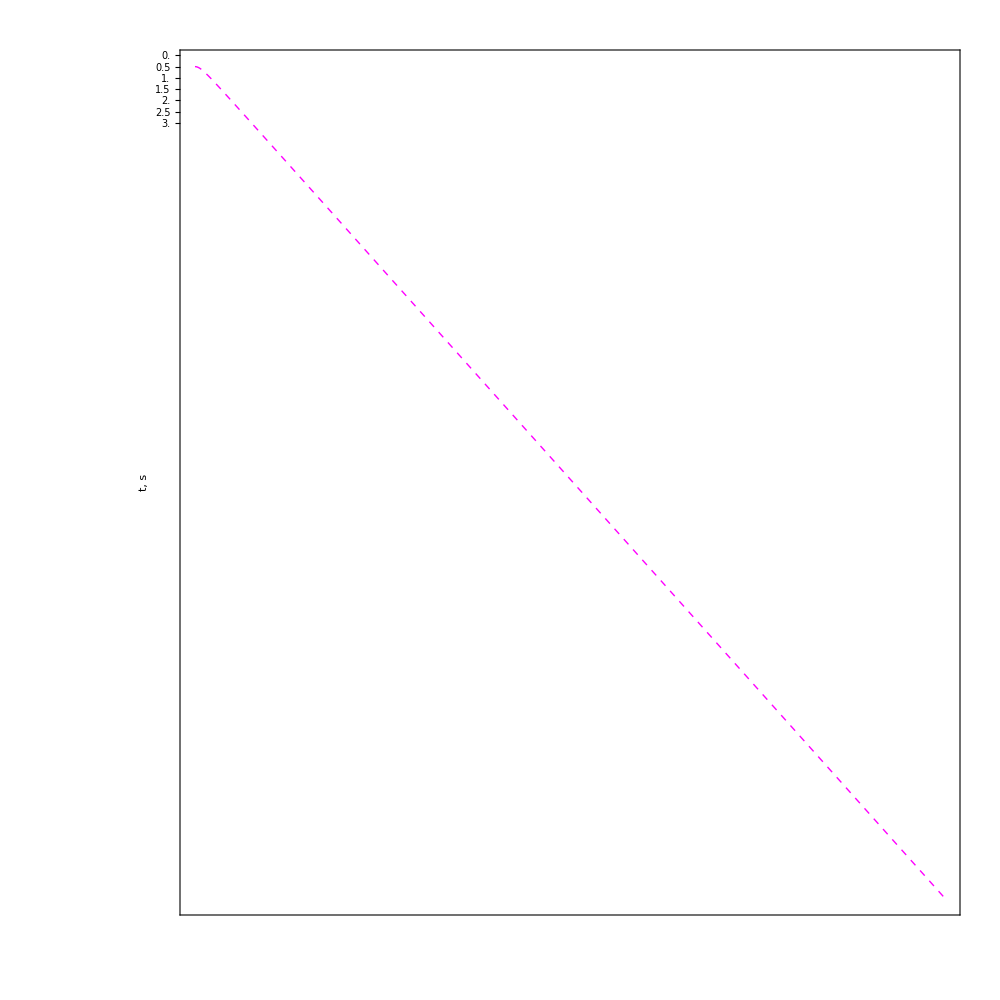

```mathematica
plot[dataTest3[[;;,1,;;]],freqvec,x,5,ωI,{2},{0}]
```

#### Plot difference between two gathers

```mathematica
ClearAll[plotdiff]
plotdiff[delta_,offsets_,t_,ampl_]:=Module[{reflTX,mm},
reflTX=ampl Reverse[ (Re@delta)/(Max@Abs@delta),2]ᵀ;
mm=MinMax@reflTX;
Module[{pr={0,2},TToptns,is=1000,tt=tlTravelTimes[{1,2},{0, .6},#,.4,.8]&,lbls={{"t, s",None},{None,"x, km"}},cfg=Blend[{Black,White},(#-mm[[1]])/2]&,cfrb=Blend[{Blue,White,Red},(#+1)/2]&,colors={Cyan,Black,Green,Orange,Magenta}},
TToptns={AspectRatio->1,Frame->True,FrameTicks->{{Range[0,Max@t,.5],None},{None,Range[0,Max@offsets,.25]}},ScalingFunctions->{Identity,"Reverse"},PlotRange->{MinMax@offsets,-pr},ImageSize->is,FrameTicksStyle->Opacity[0],FrameLabel->lbls,LabelStyle->Directive[Opacity[0],FontSize->15,Bold,Black],FrameStyle->Opacity[0]};

Print[

Overlay[{
ArrayPlot[reflTX,AspectRatio->1,Frame->True,FrameLabel->RotateRight@lbls,LabelStyle->Directive[FontSize->15,Bold,Black],DataReversed->{True,False},DataRange->{MinMax@(offsets),MinMax@t},FrameTicks->{{Range[0,Max@t,.5],None},{None,Range[0,Max@offsets,.25]}},PlotRange->{MinMax@(offsets),Max@t-Reverse@pr,Full},ImageSize->is,ColorFunction->cfrb,ColorFunctionScaling->False,PlotLegends->Placed[LineLegend[Directive[Thick,#]&/@colors,{"P, S","PP","SS","PS","SP"},LegendLayout->"Row"],Below]],
ParametricPlot[Evaluate@tt[p][[2]],{p,0,1},PlotStyle->Directive[Dashed,First@colors],#]&@TToptns,
Sequence@@Table[
ParametricPlot[Evaluate@tt[p][[1]][[i]],{p,0,1},PlotStyle->Directive[Dashed,colors[[i+1]]],#]&@TToptns,{i,1,4}
]
}]
];
];

]
```

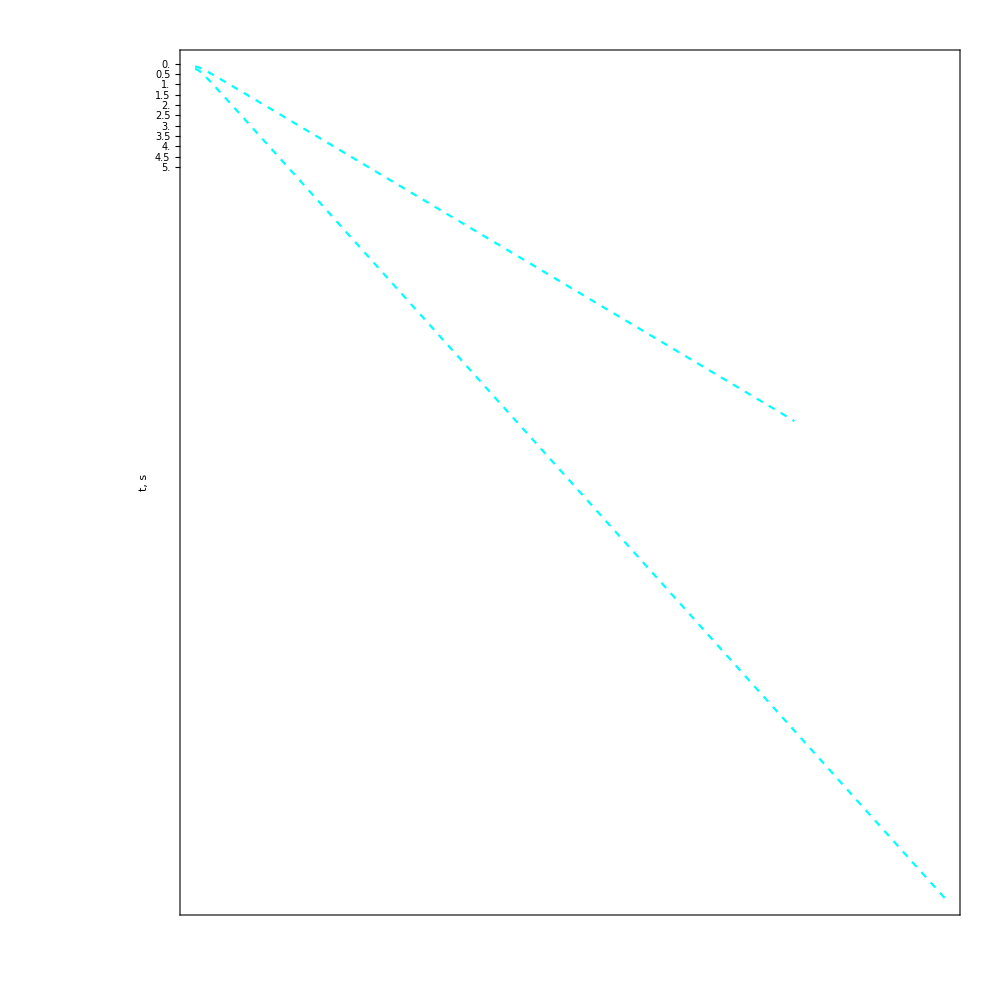
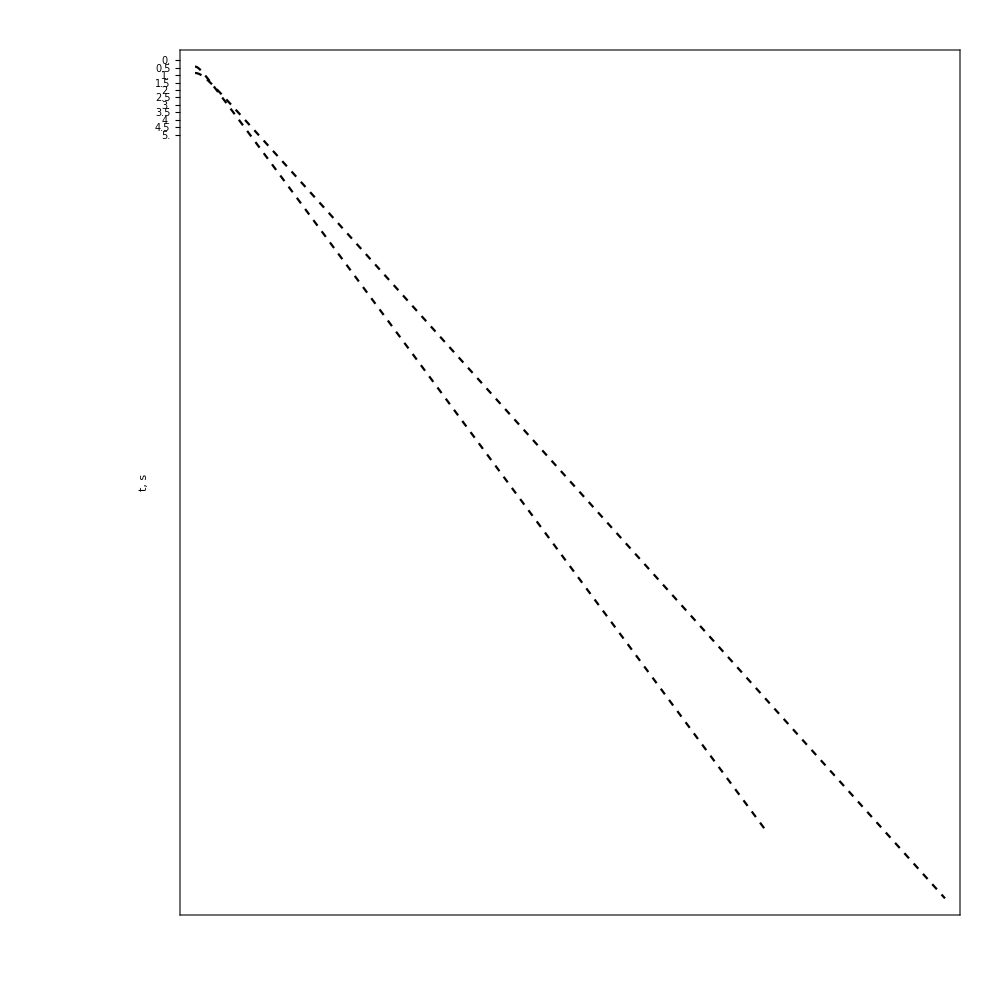
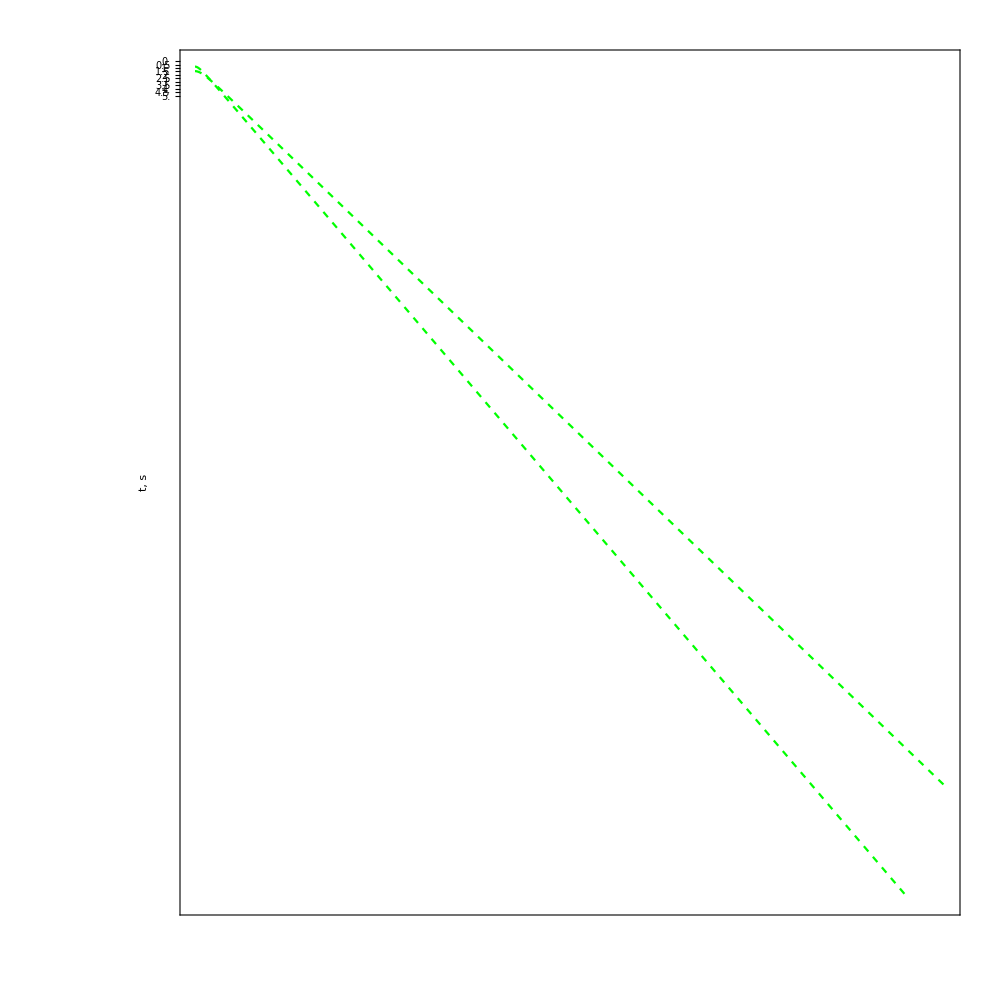
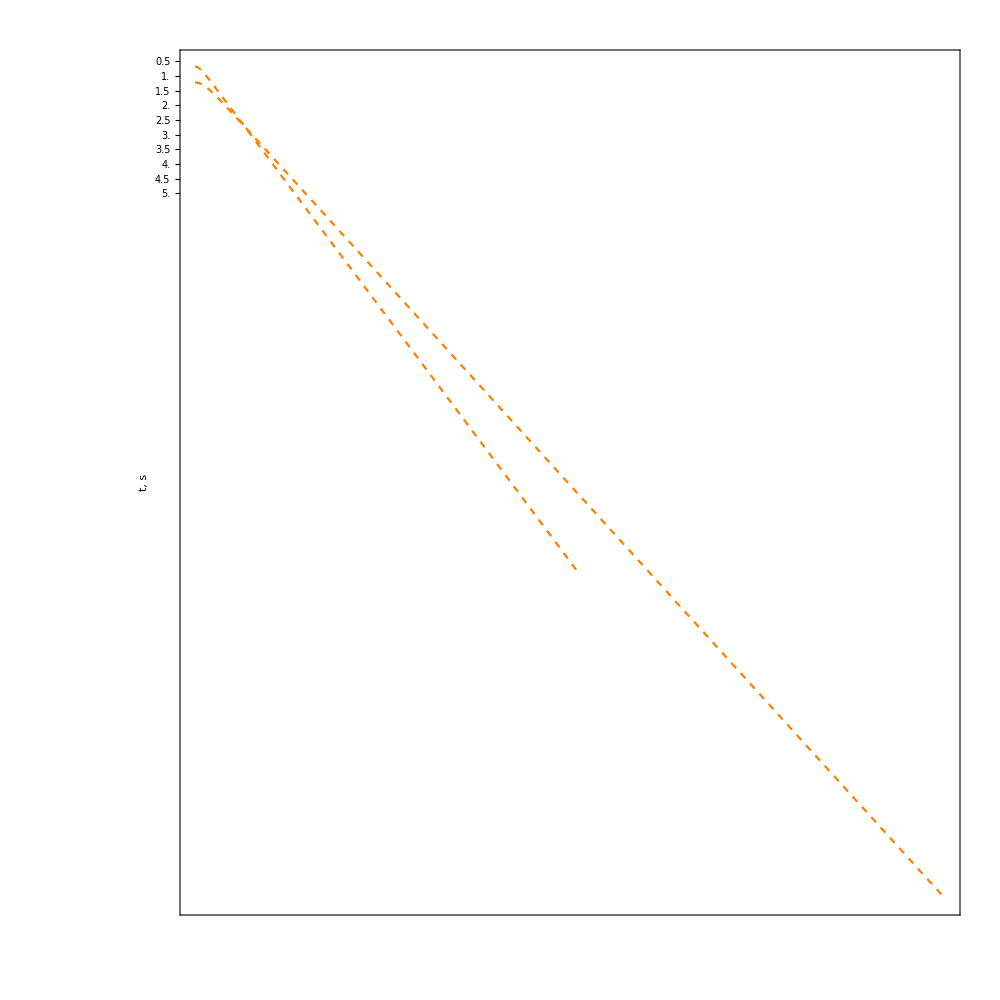
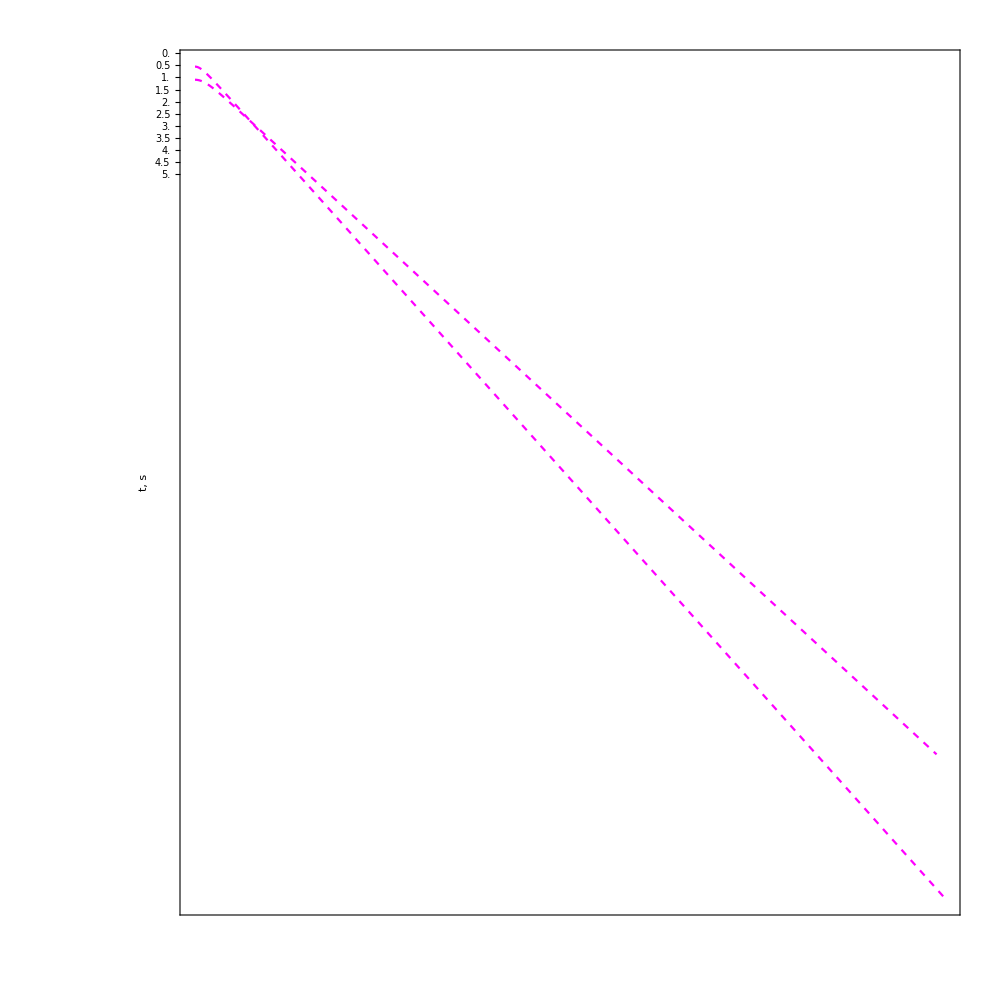
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
With[{delta=Z100[[1]]-Z200[[1]]},
plotdiff[delta,x,Z100[[2]],5]
]
```

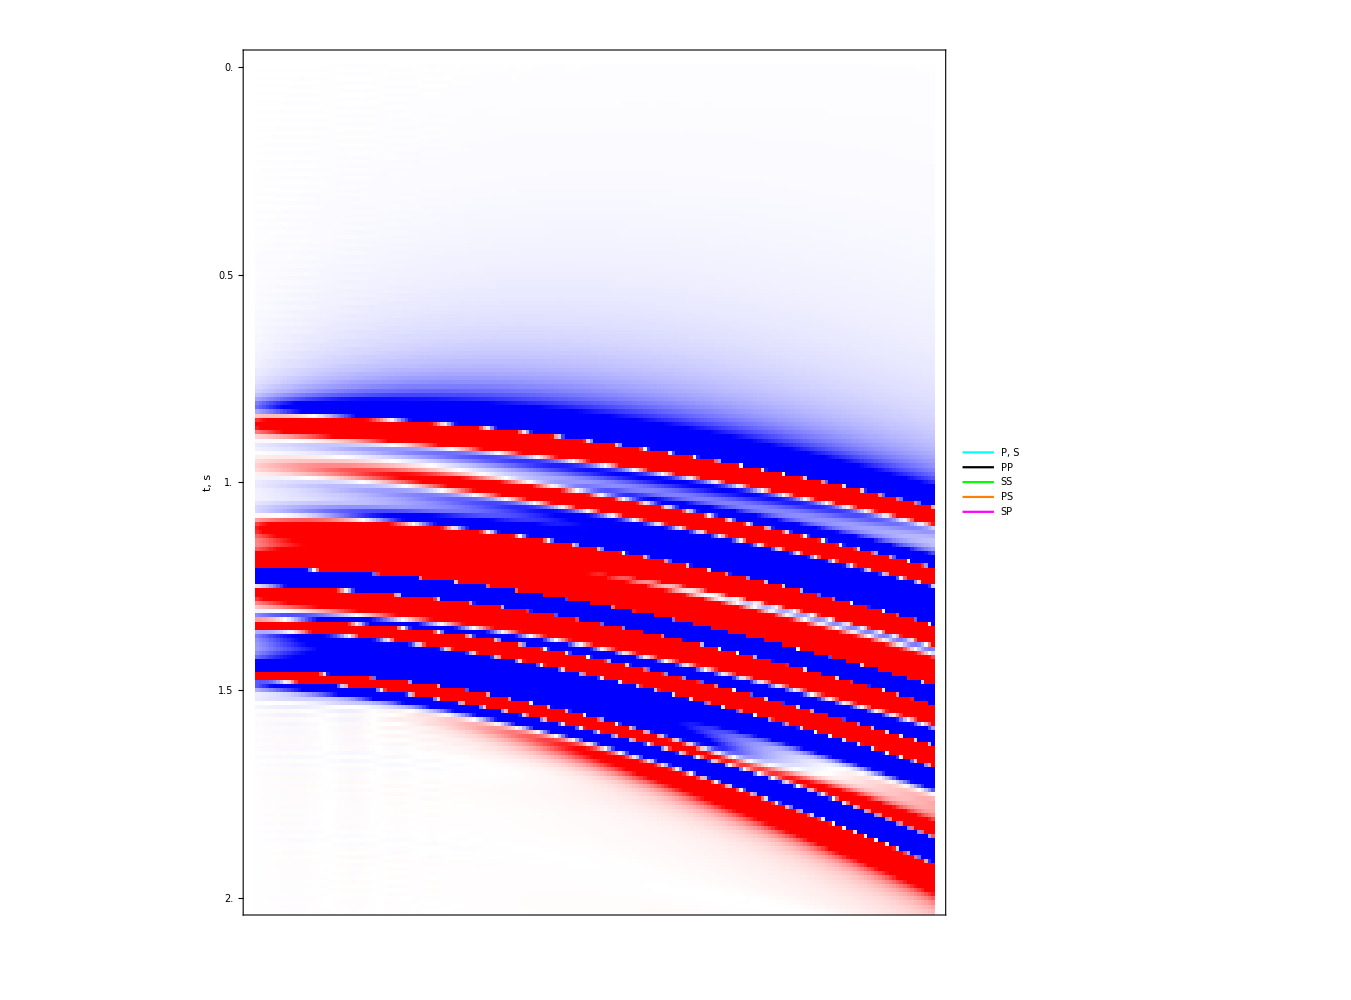
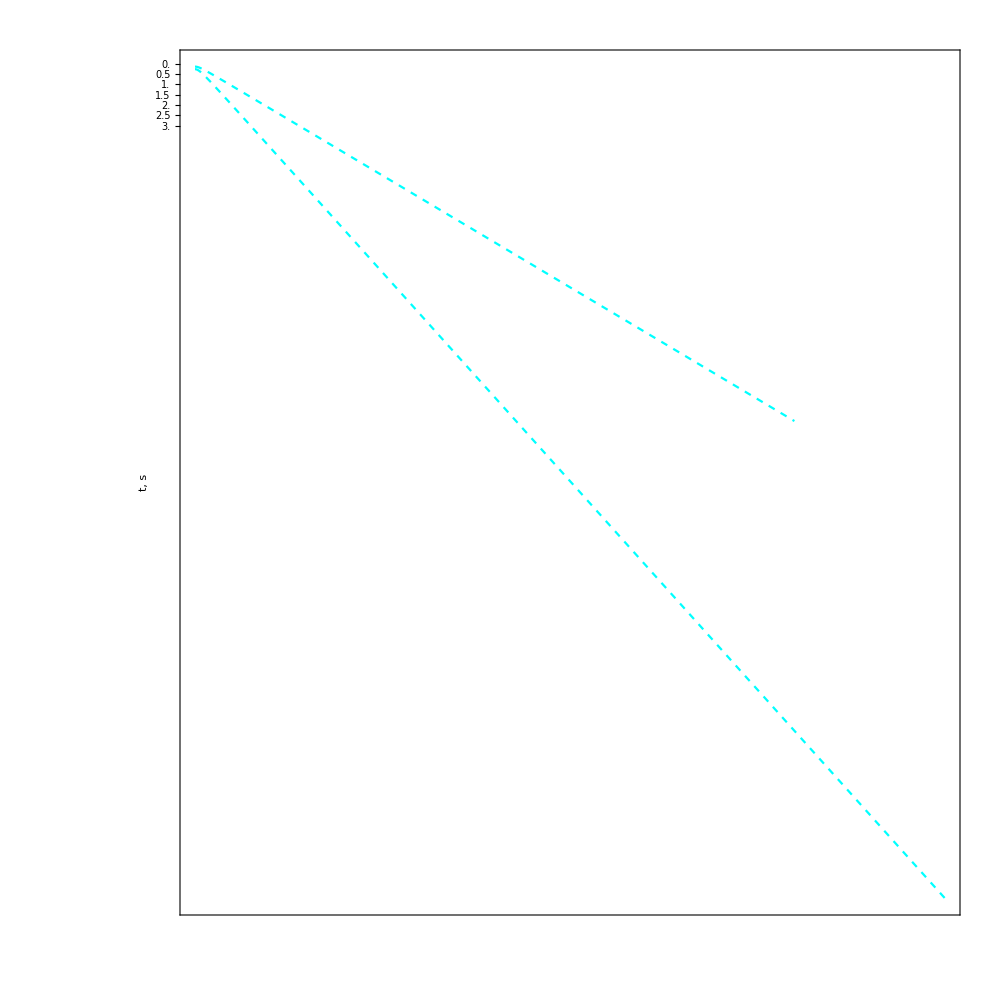
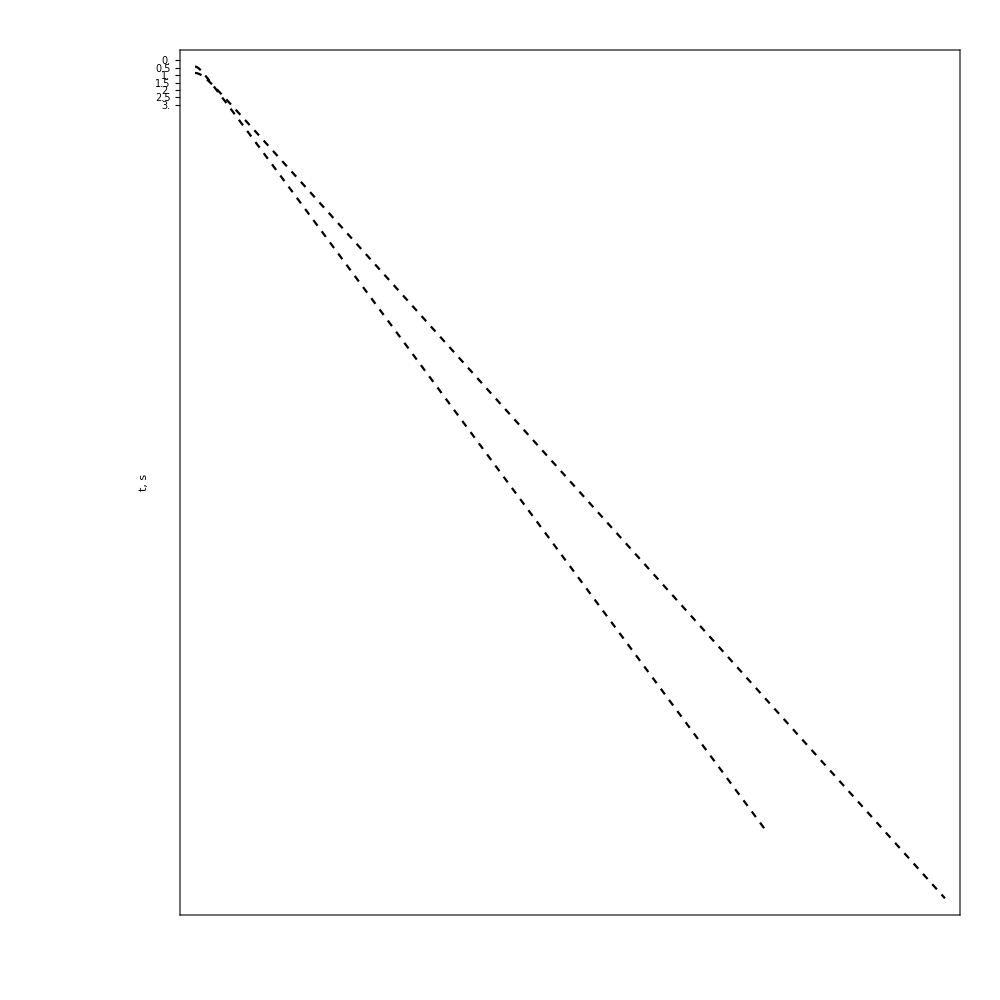
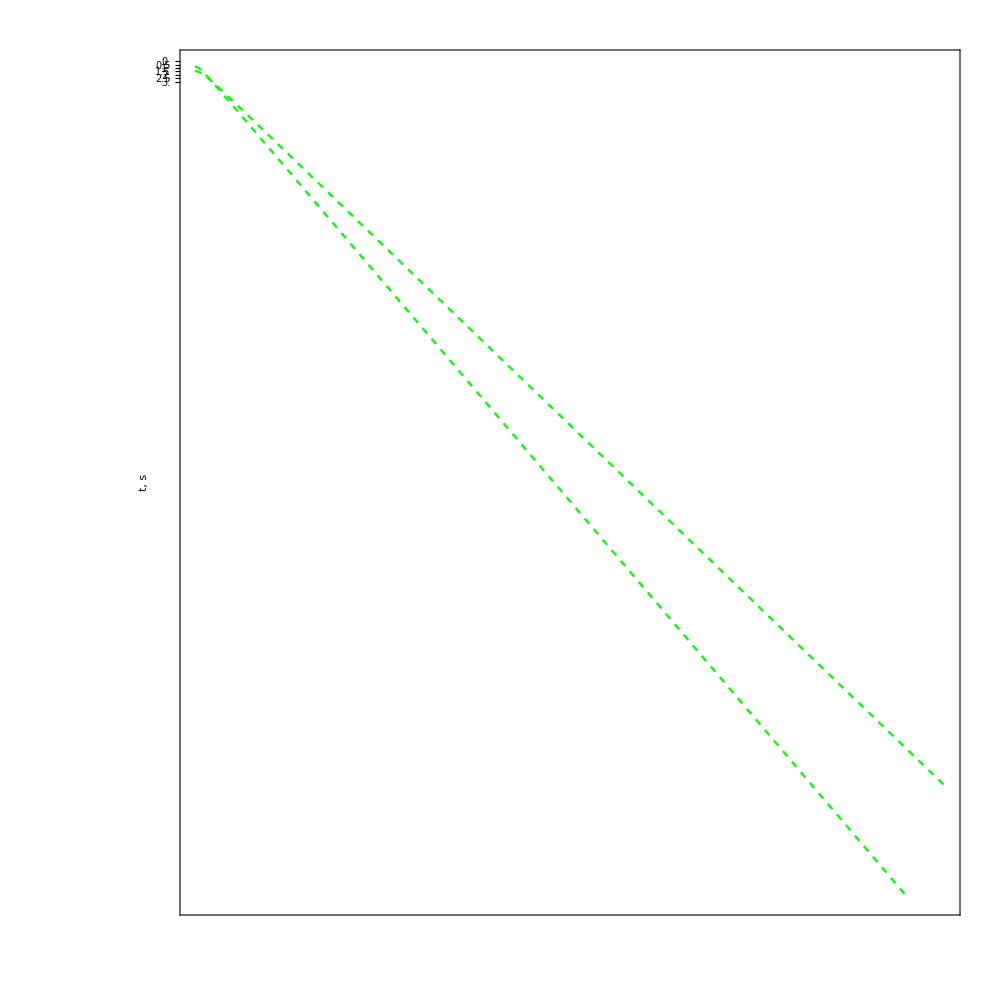
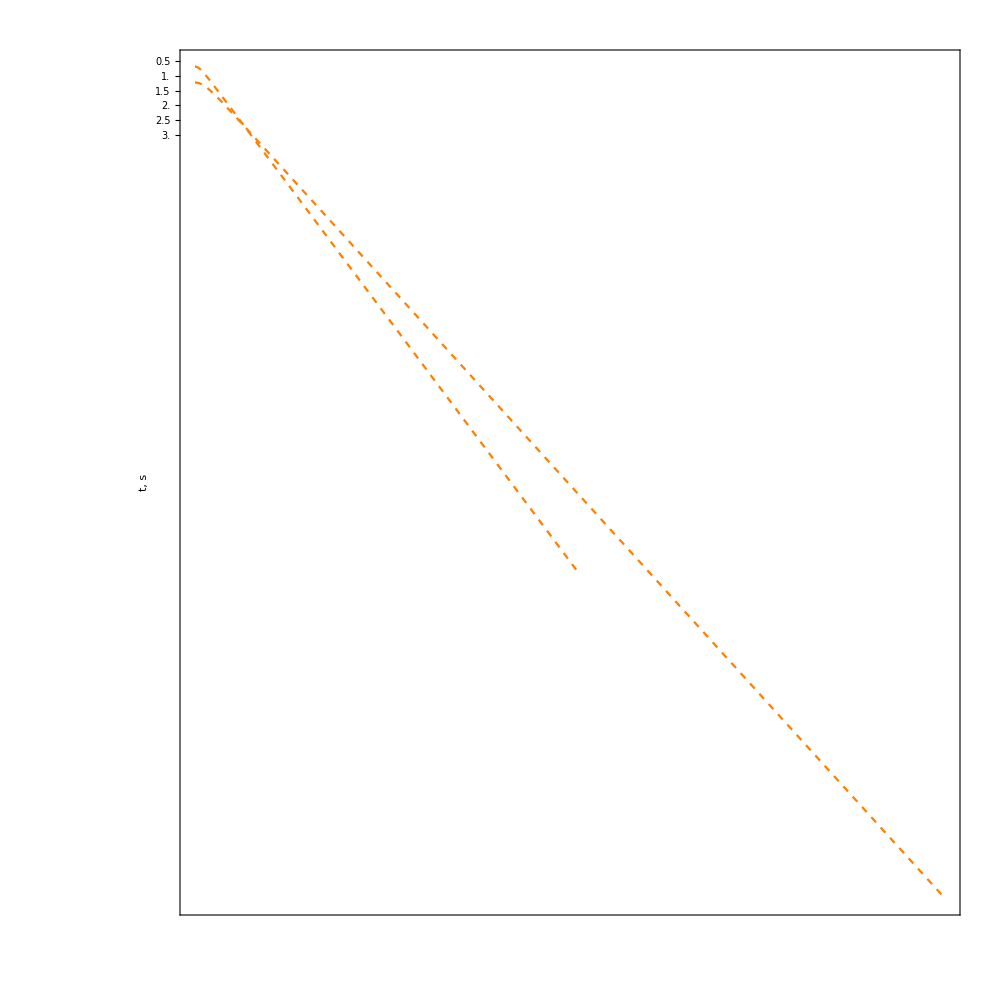
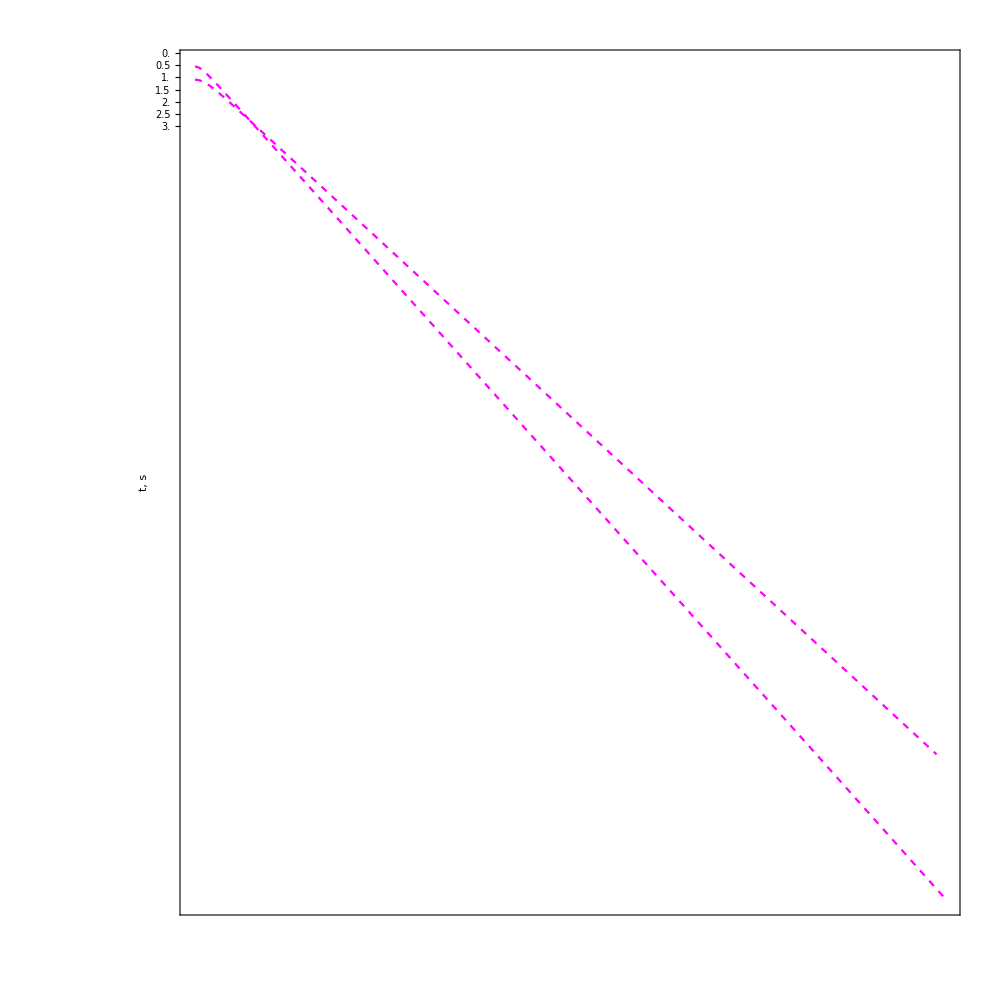

```mathematica
With[{delta=layer[[1]]-interface[[1]]},
plotdiff[delta,x,layer[[2]],50]
]
```

#### Using Shanks transform

```mathematica
computeResponseShanks[Nrep_,Nfreq_,maxfreq_,offsets_,lenrat_,BV_]:=
Module[{zs=.4,zb=.8,D2=.6,layers,overburden,model,dList,integrandp,toHTp,HTvec,deltafreq,ωList,toHTk,HW,uz,ur,pcrit,UzUr,time,ωI,Nb,test,setlayer,DIHTS},
(* ==== MODEL PARAMETERS ====*)
overburden=1;
layers={2}~Join~(Sequence@@@ConstantArray[{3,2},Nrep])~Join~{3};
dList={0}~Join~ConstantArray[D2/(Length@layers-1),Length@layers-1]~Join~{0};
model={overburden,Sequence@@layers};

setlayer[ω_]:=Module[
{λ=10.6957 ,μ=21.9734 ,ρ2=2.15,ϕ=.28,kf=2.4 ,ϵ=0.02,ϵf=0.03,α=10^-5,τ=2 10^-5,cij,vp1=2.8,vs1=1.5,ρ1=2.4,vp2=2.9,vs2=1.7},
cij=tlVTISquirtModuli[ϵ,ϵf,α,τ,ω,lenrat][λ,μ,ρ2,ϕ,kf];
tlSetLayer[1,tlCijFromThomsen[vp1,vs1,0,0,ρ1]];
tlSetLayer[2,Re@#-I Abs@Im@#&@cij];
tlSetLayer[3,tlCijFromThomsen[vp2,vs2,0,0,ρ1]];
];

setlayer[0];
pcrit=Flatten[N@(({#[[1]],#[[4]]}/(#[[-1]]))^(-1/2))&/@tlGetStiffness[DeleteDuplicates@model]];
deltafreq=maxfreq/Nfreq;
ωList=2Pi Range[deltafreq,maxfreq,deltafreq]//N;
ωI=Log[50.]deltafreq/5;

HW[p_]:=Module[{p1=0,p2=0,p3=1.05Max@Abs@pcrit,p4=1.1Max@Abs@pcrit},
Piecewise[{{1/2(1+Cos[Pi (p2-p)/(p2-p1)]),p≥p1&&p2≥p},{1,p>p2&&p3>p},{1/2(1+Cos[Pi (p-p3)/(p4-p3)]),p≥p3&&p4≥p}}]
];

uz[p_,ω_]:=HW[p]tlResponseVforce[model,dList,p( ω-I ωI)/√(ω^2+ωI^2),ω+I ωI,zs,zb][[1]];
ur[p_,ω_]:=HW[p]tlResponseVforce[model,dList,p( ω-I ωI)/√(ω^2+ωI^2),ω+I ωI,zs,zb][[2]];

Nb=Dimensions[BV][[2]];

Module[{BesselTakeUpToN,pmax,rmax},
BesselTakeUpToN[w_]=Ceiling[Interpolation[{{ωList[[1]],Round[Nb/3]},{ωList[[-1]],Nb}},InterpolationOrder->1][w]];

pmax[ω_]=1.1Max@Abs@pcrit;
rmax[ω_]:=BV[[1,BesselTakeUpToN[ω]]]/ω/pmax[ω];


DIHTS[f_,ν_,r_,rmax_,BesselVector_,shksorder_]:=
Module[{dhtlist,scorrection,list,listselect,Shanks,l=Length@BesselVector},

Shanks[A_,n_]:=(A[n+2] A[n]-A[n+1]^2)/(A[n+2]+A[n]-2 A[n+1]);
Shanks[A_,1,n_]:=Shanks[A,1,n]=Shanks[A,n];
Shanks[A_,k_,n_]:=Shanks[A,k,n]=((Shanks[A,-1+k,n] Shanks[A,-1+k,2+n]-Shanks[A,-1+k,1+n]^2)/(Shanks[A,-1+k,n]+Shanks[A,-1+k,2+n]-2 Shanks[A,-1+k,1+n]));

scorrection=Sin[#]/#&/@(BesselVector Pi/BesselJZero[ν,1+l]);
dhtlist=2/(rmax^2 N[BesselJ[ν+1,#]^2])&/@BesselVector;
list=Accumulate[(scorrection dhtlist f)(N[BesselJ[ν,# r/rmax]]&/@BesselVector)];
listselect[n_]:=list[[n]];
Print[listselect[1]];
Shanks[listselect,shksorder,l-2shksorder]
];


DistributeDefinitions["ThinLayer`"];
DistributeDefinitions[uz,ur,pmax,ωList,offsets,setlayer,rmax,DIHTS];

(*===IDHT===*)
time=AbsoluteTiming[
test=ParallelTable[
Module[{BVω=BV[[;;,1;;(BesselTakeUpToN[ω]-1)]],u},
setlayer[ω];

u={
uz[#,ω]&/@(BVω[[1]]/rmax[ω]/ω),ur[#,ω]&/@(BVω[[2]]/rmax[ω]/ω)
};

{DIHTS[u[[1]],0,offsets,rmax[ω],BVω[[1]],2],
DIHTS[u[[2]],1,offsets,rmax[ω],BVω[[2]],2]}]/ω^2
,{ω,ωList},DistributedContexts->"ThinLayer`Private`"
];
][[1]];

Print["It took me "<>ToString[Round[time/60]]<>" minutes"];
{ωList,test,ωI}
]

]
```

```mathematica
computeResponseShanks[0,2,50,Range[.1,2,.1],100,BZV[[;;,1;;2500]]]
```

{1.1891×10^-8+5.49734×10^-9 ⅈ,1.189×10^-8+5.49688×10^-9 ⅈ,1.18883×10^-8+5.49611×10^-9 ⅈ,1.1886×10^-8+5.49504×10^-9 ⅈ,1.1883×10^-8+5.49365×10^-9 ⅈ,1.18793×10^-8+5.49196×10^-9 ⅈ,1.1875×10^-8+5.48997×10^-9 ⅈ,1.187×10^-8+5.48766×10^-9 ⅈ,1.18644×10^-8+5.48505×10^-9 ⅈ,1.18581×10^-8+5.48213×10^-9 ⅈ,1.18511×10^-8+5.47891×10^-9 ⅈ,1.18435×10^-8+5.47538×10^-9 ⅈ,1.18352×10^-8+5.47155×10^-9 ⅈ,1.18262×10^-8+5.46741×10^-9 ⅈ,1.18166×10^-8+5.46296×10^-9 ⅈ,1.18063×10^-8+5.45821×10^-9 ⅈ,1.17954×10^-8+5.45316×10^-9 ⅈ,1.17838×10^-8+5.4478×10^-9 ⅈ,1.17716×10^-8+5.44214×10^-9 ⅈ,1.17587×10^-8+5.43618×10^-9 ⅈ}

$Aborted

#### Debugging...

```mathematica
setlayer[ω_]:=Module[
{λ=10.6957 ,μ=21.9734 ,ρ2=2.15,ϕ=.28,kf=2.4 ,ϵ=0.02,ϵf=0.03,α=10^-5,τ=2 10^-5,cij,vp1=2.8,vs1=1.5,ρ1=2.4,vp2=2.9,vs2=1.7},
cij=tlVTISquirtModuli[ϵ,ϵf,α,τ,ω,200][λ,μ,ρ2,ϕ,kf];
tlSetLayer[1,tlCijFromThomsen[vp1,vs1,0,0,ρ1]];
tlSetLayer[2,Re@#+I Abs@Im@#&@cij];
tlSetLayer[3,tlCijFromThomsen[vp2,vs2,0,0,ρ1]];
tlSetLayer[4,1.1(Re@#-I Abs@Im@#&@cij)];
];

setlayer[2Pi 0];
```

```mathematica
bc[p_]:=Module[{l1t,l2t,l1b,l2b,c,d,t,r},
{l1t,l2t}=Rest@tlQLmatrices[1,p];
{l1b,l2b}=Rest@tlQLmatrices[2,p];

c=l2tᵀ.l1b;
d=l1tᵀ.l2b;


t=2Inverse[c+d];
r=(c-d).t/2;
{t,r}
]
```

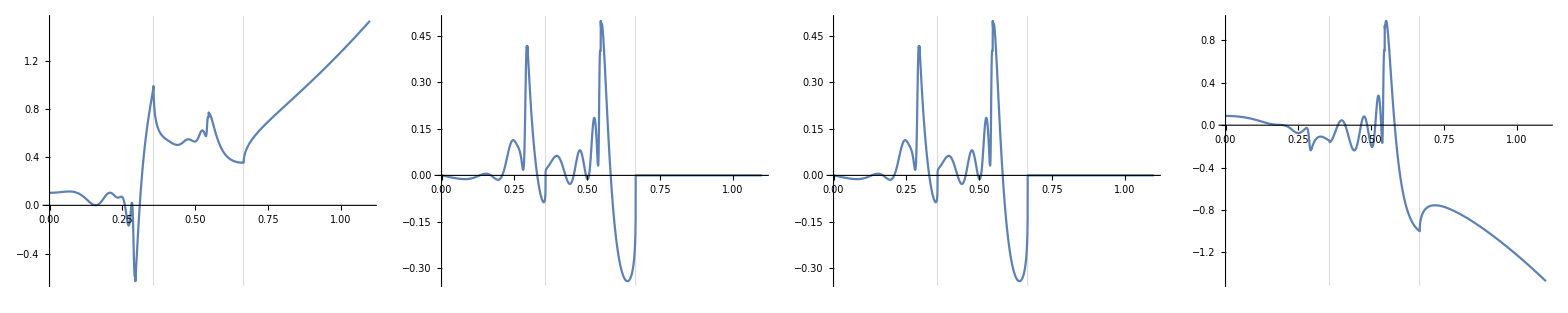

```mathematica
{Table[
Plot[Re@tlReflectivity[{1,2,1},{0,.1,0},p, 2Pi 50][[i,j]],{p,0,1.1},GridLines->{Abs[({#[[1]],#[[4]]}/(#[[-1]]))^(-1/2)&@tlGetStiffness[1]],None},ImageSize->Large,PlotRange->Full],
{i,1,2},{j,1,2}]//Flatten}//TableForm
```

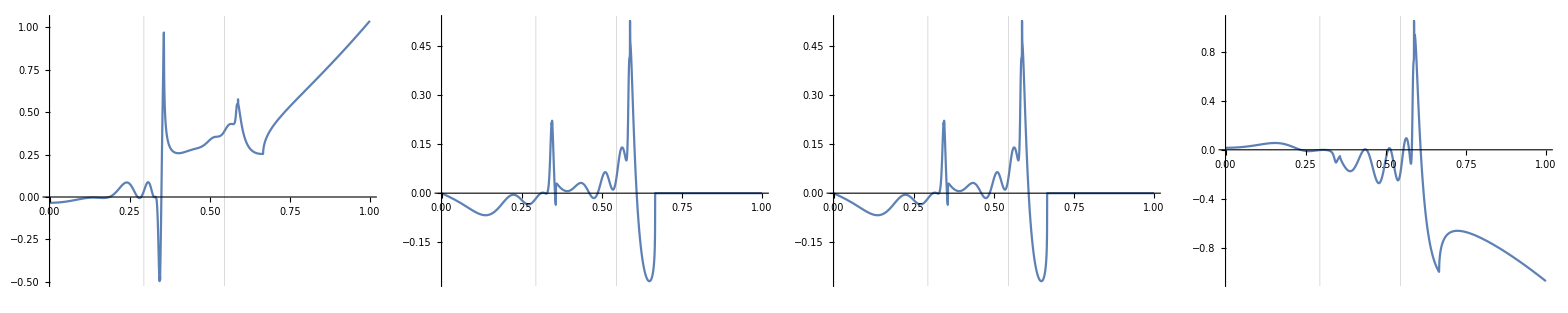

```mathematica
{Table[
Plot[Re@tlReflectivity[{1,3,1},{0,.1,0},p, 2Pi 50][[i,j]],{p,0,1},GridLines->{Abs[({#[[1]],#[[4]]}/(#[[-1]]))^(-1/2)&@tlGetStiffness[4]],None},ImageSize->Large,PlotRange->Full],
{i,1,2},{j,1,2}]//Flatten}//TableForm
```

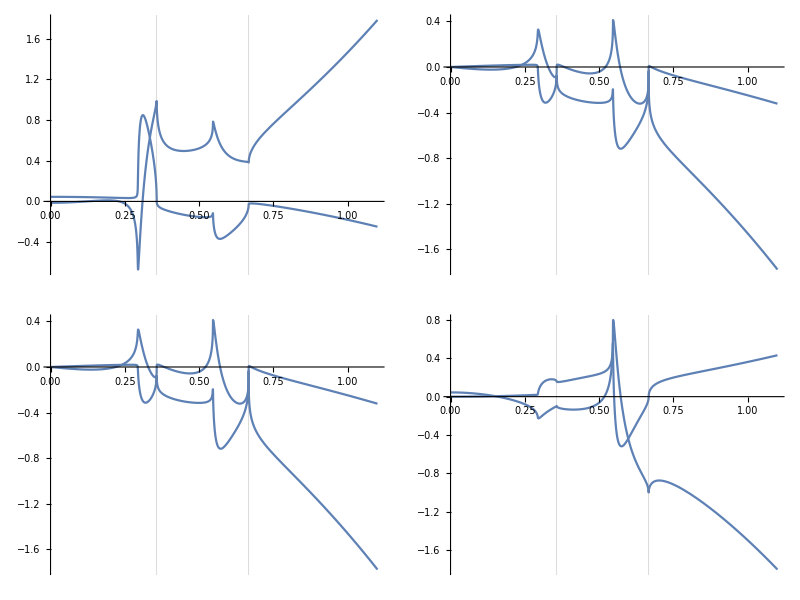

```mathematica
Table[
Plot[ReIm@bc[p][[2]][[i,j]],{p,0,1.1},GridLines->{Abs[({#[[1]],#[[4]]}/(#[[-1]]))^(-1/2)&@tlGetStiffness[1]],None},ImageSize->Large,PlotRange->Full],
{i,1,2},{j,1,2}]//TableForm
```

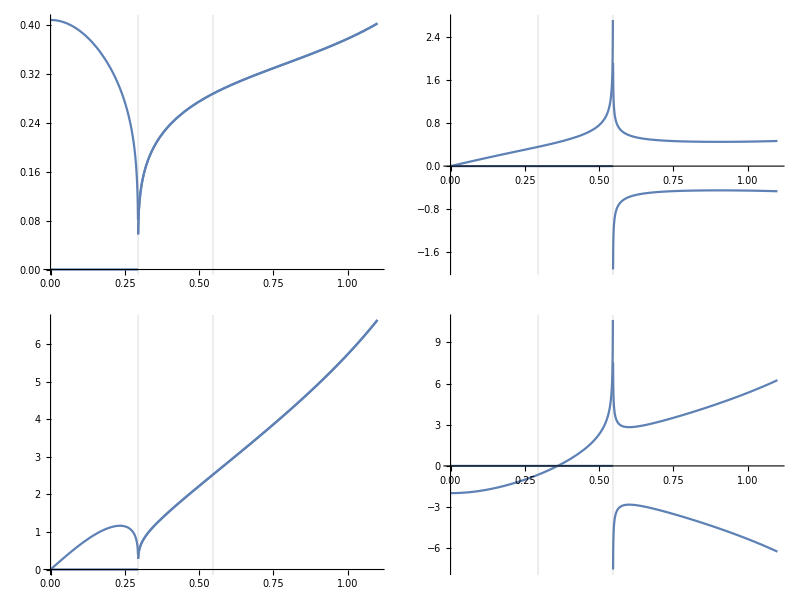

```mathematica
Table[
Plot[ReIm@tlQLmatrices[2,p][[2]][[i,j]],{p,0,1.1},GridLines->{Abs[({#[[1]],#[[4]]}/(#[[-1]]))^(-1/2)&@tlGetStiffness[2]],None},ImageSize->Large,PlotRange->Full],
{i,1,2},{j,1,2}]//TableForm
```

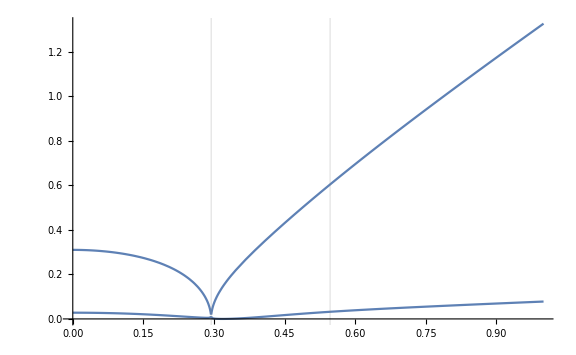

```mathematica
Plot[ReIm@(tlQLmatrices[2,p][[1]][[1]]),{p,0,1},GridLines->{Abs[({#[[1]],#[[4]]}/(#[[-1]]))^(-1/2)&@tlGetStiffness[2]],None},ImageSize->Large,PlotRange->Full]
```

```mathematica
tlReflectivity[{1,2,3,4,2,3},{0,.2,.1,.1,.2,0},.1, 2Pi 50]
```

{{{1,0},{0,1}},{{-0.605512+0.795836 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-0.742304+0.670063 ⅈ}},{{-0.587552-0.809187 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.802936-0.596066 ⅈ}},{{-0.444121-0.895967 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-0.358954-0.933355 ⅈ}},{{-0.605512+0.795836 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-0.742304+0.670063 ⅈ}},{{1,0},{0,1}}}

{{-0.376796+0.229076 ⅈ,-0.0364124-0.253245 ⅈ},{-0.0364124-0.253245 ⅈ,-0.467099-0.0618661 ⅈ}}

```mathematica
(*

(*==== MULLER ====*)

U[ω_,k_]:=Reverse@DiagonalMatrix[tlQLmatrices[overburden,k/ω][[1]]]+DiagonalMatrix[{k/ω,-k/ω}];
J[k_,r_]:=DiagonalMatrix[{BesselJ[1,k r],BesselJ[0,k r]}];
Su[ω_,k_]:={-k/ω,(k/ω)^2/tlQLmatrices[overburden,k/ω][[1,2]]}Exp[ⅈ ω zs tlQLmatrices[overburden,k/ω][[1]]];
Sd[ω_,k_]:={k/ω,(k/ω)^2/tlQLmatrices[overburden,k/ω][[1,2]]}Exp[-ⅈ ω zs tlQLmatrices[overburden,k/ω][[1]]];
ref[ω_,k_]:=(DiagonalMatrix[Exp[I ω tlQLmatrices[overburden,k/ω][[1]] zr]].tlReflectivity[model,dList,k/ω,ω].DiagonalMatrix[Exp[I ω tlQLmatrices[overburden,k/ω][[1]] zr]])//Chop;
integrand[ω_,k_]:={{-1,0},{0,ⅈ}}.U[ω,k].(Su[ω,k]+ref[ω,k].Sd[ω,k]);*)

(*U[p_]:=(*Reverse@DiagonalMatrix[tlQLmatrices[overburden,p][[1]]]+*)DiagonalMatrix[{p,-p}];
J[p_,ω_,r_]:=DiagonalMatrix[{N@BesselJ[1,p ω r],N@BesselJ[0,p ω r]}];
Su[p_,ω_]:={-1,p/tlQLmatrices[overburden,p][[1,2]]}Exp[ⅈ ω zs tlQLmatrices[overburden,p][[1]]];
Sd[p_,ω_]:={1,p/tlQLmatrices[overburden,p][[1,2]]}Exp[-ⅈ ω zs tlQLmatrices[overburden,p][[1]]];
ref[p_,ω_]:=(DiagonalMatrix[Exp[I ω tlQLmatrices[overburden,p][[1]] zr]].tlReflectivity[model,dList,p,ω]ᵀ.DiagonalMatrix[Exp[I ω tlQLmatrices[overburden,p][[1]] zr]])//Chop;
(*f2[p_,ω_]:=ω({{-1,0},{0,ⅈ}}).U[p].(Su[p,ω]+ref[p,ω].Sd[p,ω])/4./Pi/ρ//Chop;*)
f2[p_,ω_,r_]:=p(J[p,ω,r]{{-1,0},{0,ⅈ}}).U[p].(Su[p,ω]+ref[p,ω].Sd[p,ω])//Chop;
*)
(*
ref[p_,ω_]=(DiagonalMatrix[Exp[I ω tlQLmatrices[overburden,p][[1]] zr]].tlReflectivity[model,dList,p,ω].DiagonalMatrix[Exp[I ω tlQLmatrices[overburden,p][[1]] zr]])//N;

(*==== URSIN ====
stress-displacement as in Stovas and Ursin:
b = [ω Uz, -Sr, Sz, ωUr] ;
Tranformed back to space-time:
b = [uz, σrz, σzz, ur] ;

*)

Σ1[p_,ω_]=1/(√2)tlQLmatrices[overburden,p][[2]]ᵀ.{-1/(ρ ω) ,0};(*σzz force*)
Σ2[p_,ω_]=Σ1[p,ω];
S1[p_,ω_]=DiagonalMatrix[Exp[I ω tlQLmatrices[overburden,p][[1]] zs]].Σ1[p,ω];
S2[p_,ω_]=DiagonalMatrix[Exp[-I ω tlQLmatrices[overburden,p][[1]] zs]].Σ2[p,ω];
U[p_,ω_]=ref[p,ω].S2[p,ω]-S1[p,ω];
B[p_,ω_]={Sequence@@((I tlQLmatrices[overburden,p][[2]])/(√2).U[p,ω]),Sequence@@((tlQLmatrices[overburden,p][[3]])/(√2).U[p,ω])};
b[p_,ω_,r_]=p ω^2 B[p,ω]{1/ω,-1,1,1/ω}{BesselJ[0,p ω r],BesselJ[1,p ω r],BesselJ[0,p ω r],BesselJ[1,p ω r]};

(*{ur,uz}*)
u[p_,ω_,r_]=b[p,ω,r][[{4,1}]];
(*{σrz,σzz}*)
σ[p_,ω_,r_]=b[p,ω,r][[{2,3}]];
*)
(*FindMaxK[ω_,tol_]:=Module[{kmax,phase},
kmax=phorlayer1 ω;
phase[k_]:=(DiagonalMatrix[E^(I ω tlQLmatrices[overburden,k/ω][[1]] zr)].DiagonalMatrix[E^(I ω tlQLmatrices[overburden,k/ω][[1]] zs)])[[1,1]];
FindMinimum[{Abs[phase[k]],k>0},{k,kmax},AccuracyGoal->tol][[2,1,2]]
];*)


(*With[{p0=.1,ω=2Pi 20,r=.3},
tlResponse[model,dList,p0,ω,zs,zr]
]*)

(*Module[

{Np=5000,pmax=4,pList,dp,r=.3},
dp=pmax/Np;
pList=Range[0,pmax,dp];

DistributeDefinitions[pList,ωList,dp,integrand];

freqvec=ωList;
AbsoluteTiming[
testZ=
ParallelTable[
dp Total[integrand[#,ω,r][[1]]&/@pList],
{ω,ωList},DistributedContexts->{"ThinLayer`Private`"}];
]
]*)


(*AbsoluteTiming[
testZ=
Table[
tlDHT2[Noffsets,ref[#,ωList[[i]]][[1,1]]&,0,pMax],
{i,1,Length@ωList}];


freqvec=ωList;
]*)


(*Table[
Module[{ω0=ωList[[i]],testk},
{testk=FindMaxK[ω0,11],ListLinePlot[Transpose[ReIm@ref[ω0,#]&/@Range[.5testk,1.5testk,testk/100]],ImageSize->600,PlotRange->Full]}
]
,{i,Length@ωList}]
*)


(*With[{ω=2Pi 300, tol=10},
K=FindMaxK[ω,tol];
{ref[ω,#]&/@Range[0,K,K/(Noffsets-1)],K}
]*)


(*With[{ω=2.Pi 150},
{ListLinePlot[(ReIm@tlDHT2[Noffsets,ref[ω,#]&,0,kMax][[;;,2]])ᵀ,PlotLabel->kMax,ImageSize->Large,PlotRange->Full],
ListLinePlot[(ReIm@tlDHT2[Noffsets,ref[ω,#]&,0,FindMaxK[ω,11]][[;;,2]])ᵀ,PlotLabel->FindMaxK[ω,11],ImageSize->Large,PlotRange->Full]}
]*)
```